This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 2 Plotting Central and Annular Branches ch2BranchPlots.nb

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

1+w^2-z^2

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(4+1 z^2)+(3/4 z+5/2 z^2) w^2+(-3/4+1 z) w^3

3

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=5;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
$implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
$implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
$implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
$implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
$implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2: Compute/Retrieve singular data

### Section 2.1: Compute singular points

```mathematica
$workingPrecision=1000;

at=AbsoluteTiming[{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=getSingularPoints[$theFunction,$workingPrecision,True];
If[$theSingularList=="-1",
Print[Style["Encountered error with getSingular Points!",Red]];
Abort[];
];
];
$singularPerimeters=$minRadiusArray;
$singularNorms=$rNormArray;
$singularDistances=$nearestDistanceArray;
(*
 add 0 for TestCase0006 for book
*)
(*If[subDirectory=="testCase0006",
PrependTo[$theSingularList,0];
$minRadiusArray={1/3,1/3,1/3};
];*)
(*
 add 0 for testCaseFInif
*)
(*If[subDirectory=="testCaseFInif",
PrependTo[$theSingularList,0];
$minRadiusArray={1/3,1/3,1/3};
];
*)
If[subDirectory=="testCase0001Inf0",
singPerim=1/3 Abs[$theSingularList[[1]]];
PrependTo[$theSingularList,0];
$minRadiusArray={singPerim,singPerim,singPerim};
];
If[subDirectory=="testCase0400",
$theSingularList={0,1};
$minRadiusArray={1/3,1/3};
$poleIndexes={};
];




Print["Total singular points: ",Length@$theSingularList];
Print[Style["Time to compute singular points: ",Red,Bold],at[[1]]];
singPrec=Floor@Precision@$theSingularList;
If[Abs[$theSingularList[[1]]]<10^(-(singPrec-$acf)),
Print[Style["Zero is a singular point",Bold,Red]];
];
If[Length@$theSingularList>1,
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
N[$theSingularList[[1;;2]],20];
];

 Export[singularDataFileName[$theTestCase],{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}];
```

Time to compute resultant: 0.0008935

Time to compute singular points: 0.006446

Total singular points: 10

Precision of singular points: 1000.

Total poles: 2

Pole indexes: {1,8}

Total zero points: 2

Zero indexes: {2,3}

Min singular perimeter: 0.158927

Smallest singular points: {0.,0.-0.5 ⅈ}

Total singular points: 10

Time to compute singular points: 0.040124

Zero is a singular point

minSingAccFactor: 5

### Section 2.2: Retrieve singular points

```mathematica
(*
 retrieve singular points from disc
*)
If[FileExistsQ[singularDataFileName[$theTestCase]],
theData=Import[singularDataFileName[$theTestCase]];

{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=theData;

Print["Total singular points: ",Length@$theSingularList];

Print["Precision of singular points: ",Precision@$theSingularList];Print["Total poles: ",Length@$poleIndexes];
Print[Style["s_p indexes: ",Red],Style[$poleIndexes,Red]];
Print[Style["s_z indexes: ",Red],Style[$zeroIndexes,Blue]];

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
If[$theSingularList[[1]]==0,
Print["Smallest sing power: ",N[$theSingularList[[2]]^maxZ,10]];
,
Print["Smallest sing power: ",N[$theSingularList[[1]]^maxZ,10]];
]; 
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
,
Print[Style[singularDataFileName[$theTestCase]<>" not found during import.",Red]];
];
```

D:\algFunctionBookVer13\data\testCase0017\singulardata.m not found during import.

### Use AsymptoticSolve to compute series

{45.0828,Null}

(-1.03078752567445731922036302713958402167206294512565620770068252843097350518763810105414591305996393751265667937377068716760248588019215124518737570479914369371256869707363246996328770412742301122583746761198265128500061526025770251520674604136490677330866184617737903763065260096381405333298305432940823767067829813150402275085740325559160243423449055003105286944997647596223266117594962644957664032538710450761250089767638401101618263977477910055761128937241530074781583576275993611124032275829470821633266302172152999054800611178015363923380388979777703283069818292699330969522933285297524098829780490891962354979426796240929843503096040446889205554311150081465896528715736737692181865983840100888484089029744904533196013391138394046150909684299558660309153214470173882440355320065351354286859411986199795091531391932658407284558027327390551277111266911728297043863156292157181576920756314873004350933647739605887037926710044331327004313439831187887524991663076180852618824640961864275724737112687639635168681031+0.10489161204031145673306123259607605442325038762405562366907837400001917669638419999477133201731245582919378579906860488191264201712870324337808885203165147817107643301034829764945122888851332774428917393106661076129738544803731608352828595951616003424031810556699859956460453732037796297759574207887119893717443948475079184060303609181934991390716427236093241918794031322786459389045352868292120278358349189434794109212177091308899057471818248278253673673003432560814174156424390687593843534411123417424600002437201135373496932702267167227497058120485668915675724428057514319585430194679316485285750012226322227097923120874597517088941116115217798140560212713269282527012180387261881890164454287968836676652395712746701992419056197281926659674617359227597999482882013460496324930997761739126435717075519704833181107253454885512005710208380891645117982694495112819872248810763593626576414103093598888908291063757175131264650805913397369507916147826195272404845829453966433267842228933107756761313547727566252208145 ⅈ)-(0.4571013197266286875690156059730980841911020517404015599083737596924492196689963894782708531554625919041568534487666128614020432478975188331739205552844538642542914484647152371033578400318535537294697033069858860191071515813352228384841083198177572186706214174187659035542548190002354047738950900163129317582076855005546575209744255628631800600493051493129989270897437139270084599083042603641842968108389646934882806280713504017208183722749811354963466239622009660980217822373745182472720477573392540351051763892256045269271592426071679216002135703323591936769054782302482130693163137428347839675143768874447276598309237675397523579645771512859775432804430672809717346104835655573502313696757618608623244631064644559200827892420779962524409710908697485856532328127715338311424913595694264237845778356962696610139891689042215432165899857506052034026307636517442195246013779095942281065920625922471920947791020637480768060995979246124800415950316457700051008972694631974766498546498677984779472629828068141485794-0.06090126749259226284607911665439478804645125626243943987913439619236438008663998351812163153344701953338473860066755552039971700527299011007816198227066054447331146407168901998756416710063332623075455192384289424514992132888221452509400827891559803110887520569145330449163269975728100256629614205451465915823910734938242061821363300183981125999953039276110359952271848143012684970514187247730367688063559265376086537209106392064690702362167254443000852550459193089620854124494010632651970836193250062531062710556551311771017311854145440230917278339047801038049059388665582485810161265803614771838470637592574300557049772656387375287193840281383093605611954652280418305507054799589799924502139971558340386275745728457454940697368004387688529694328977989075867147329535823398264670808893609462969941245519880532977766728624379004781919829358510638762100731820106884074139179975804084610843169751003181044124212667864487876401456820140278065797032731936296447031702680195434972438018266104166503112826619786049858 ⅈ) ((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z)-(4.50601559333702331263286078591312417961690382179837578359679369715972505231825834184963928486512003563051266890154352917602266132657151893371208452336881792307113499934265380402784087790758715444215899505024875543316061000916555363292743029935767529758215784331992503239161568031405624540138303845095221540827884478048088778437066393095549768253522118292027634451325570648971140787091615415515216674784793851018836040439780218430524632457887869348304029512001907539540573168074450765433224617687597681047009746077084693222754976461876328030416963577550631513367146884897670118804955004686933351069360927720689233593917963470856250813582658811907511550924978819268597920145503857468583955765369262955998920504966936961662077065977101110419704361654570684024042547872875563492887525236606503138246356525560178056828777355574891543329005327645091787158130144029949262580725877924949156849248056304935667491683227078859166843398426503152794768810712806883037823831012471864476592615120128216435841882803194500759-2.14195430313680038570464420287156330884915468003995103096524898323880224163338081223309932522485835650685015628365130134042676655333796579995944647590958315375362016685374073537816279464784543853001260083906189951385053120772213060596463141768783090514020410335407350126496772046209097874320572245778498478439174703791587591148078889287630119233283571709456989508768021612784215986888189133564379122423053294595529743060146111078708033921745204341295250551149712730036556424080930603720115282046132409676647385924127643790535374145434346506410599494650095131502104671368893141438036031201226661798985733710425814925482462170772946598123737717059987959837233621702781864612780041224651984139892562157127776593273900828703277714354775172618240760576005598301805658983222009467071989459840288407462736262054324500864022932595357427177405201831785475649032025003504120370692409226579646605913207976496774688662521969232559697469641086236241040390731849947853038616131105438192421873212774936358973554590116591018 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^2-(1.501324907012804852253108285031894071677413928022324801913106518053765903413387135279836507893721286301998093616558192903525613598178875992729512063381348525937316809688387499218634944301283090691626794092316126527684299996414270670672611960228439054284764050345162445419144578889177964280984922502600452657729619897967579085751484725401348383276337435878801883604916363121488669328699365547399517120862680787683623243335403482200985124485950856842963452396867977240341465161569438342166527435423171536147863469438416158421452209405732702556849319650856035020706015143487627679802967712091273699865057579850071889560692544959912169079502105415904766425648141616746642492656968770915734097076389201788898014666712044022401744680266493248564936833139095681965021998783634334214455317584142031170887368847578485283031862340563064403647119717899287177658436838158185535695252222002771393899416252836306353328315545520211032828054590495558706580368438052220995021861715579320041498948026304574273583219146852533-2.163022430420441385681093060971714733550994088273991866948263222361510176617277516856992811969938059657279820693990979795145638501382857348238458527976598880819329186848358779527846628276430372265409417223825897358420388842605214697874366618462738191347845685513991345860451383031348820646999178555199629797325471100174650524278380590898642365467680513995965798234398192935463566172562483429256468758334585434391272822237054564754170555579928443436836276874309119142277466100572239200279626532809289668615342941065763687288112941875747012455906867329960774704570927766837105375119367499580666804249687446283291789013853634478610684601955661281751005426224429630132598265622766948246853433449235129466347353376974298981567322146302004555186462812675173551715773604405919199639181298301721315345947660227756972891508396146083523981357415999199096390247802937570091765799554416175816237238397506360677984955860383733419963109632513102821102385753002733057934581728448304007057148054147330904646770661673609721 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^3-(4.728323090850902394952682360396189538912340520226400665681449682297436699193308805358925759860435129827316143136367245941405056516578332861383568152278066106976914765363605982471206288127716298137400937788436817973940724574426408850907265159076261586212523226264887468563903707217483803961627702722469974408957449636957916610800430194273104611653764585733388320175288242139404739002342389401476947641685829531034934543030832349498492143516635506007589851688335122343791534634730802746167388658793193498779629164851063354318194323381135174766959167377506118903270138968392734673458073575089443993767635276073701485022945308636788254944828623681826031302656547912160562406737873698935130851824576925509436948175430455447941519070597525484173371349117416348482880398644842783386338541684354020368602448229933085911957133590709500340476256621445038950439854455585246101024836961502803375667237051902851234655738434237855308580744545940380742592689700997072660359171843996211545702903834327290427142038418448+317.3692931206124134054968789884011416875740495422167125367627142705229535753702541828215708418257732741421462845295639446233727605007607000160063509270121271369091757233856003203433981858404037320343164455659512274828158770586228335897917180429086051924926823909154795723838357582729082025762818990279872228890916919997040270170863892459586018868801425678222709271547863190589487231091852557587602512173214009508565825989874862414305137833140296311291567520096227397149458490797356068110349120543189361837919851374624265947461037145842739854909092719910673296165407021463020429076111506184869156205983061314816267630516169305034374287502621557897752964855591168416946326778130856600110676700470513369274662502912343190403697524228307502148675030695538244763152357880393137271072407260267986362514114481295454942276910359827422391150457888485184329575830949390042900645116112519078795931276835669440159531334512056420568777271056051629083040430892806183739219278460800894580277972334419124753793923634870343 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^4-(1507.07514535659155282549918838100347528124120991362671333687692972671315485556023297701847981656037367166010168356119642017373879365007687425459450418891907312255754571512540592960205331955121782457851124106022792759811709655671988183805461871435437988363998068054932844735839246922560876363422139384593520324907101428341934288200595957257293064198131724843287633381822361107931451365559729086960344004821789341958262866267644173859587758363575704089121372556148200324399297066156530710950227670362148996901667395970962371490509462003066963402242659449741651710703059582115486609805414261116501260476556187386024626891519796174318251812273851665768335753642854010112258423125871101978274254449336414013409509567164892987762600140086565642281395527911935982119722585564309699775975910400448629569930651469067445759228600293761229352765325614863609638234228601881888324167966386052023490928797089841693045293236491227631327424171025202447430021467901633710703880143464901707679122058533268533632123955433472+699.797504134967684089429061474992142444468041123681467680174397028420125812316249150070631682982447491517767018657087951265821473761950358688873955030808370702509343565729825676009495934772154602647021703570573085400462207659530174179816157144525206139460954787457673539477176896834814807562061613800745247167331480630270267588380486207174136580406962415135024031212608136068515076806435575706831524042254301272666697824072127320160948056869535033796180068008663544020738630825840048862409593945505434200283323125820148910900357008254262104628106878168154279411569768938791797332997309527482321673495513248422324876097804720136266570125832468356185980686981986203917047923904944337021949479669760850179769669271836180191583038596994721008633370390364339597074166395418627009753107485330622992390578255218068402215304124479315662322858881301153356447421885491585421189583076274461863880636901933506266101026004354953742881620050979219141083820212451161632256253632008795038891778716344182170384590507185904 ⅈ) (((0.9291082476915902106730977768710446786784083372531918127273974812875229241757181968257053085919547937386433459468504511690569306370771376687442786131966623542861018520405831573457158786480061568051421305628557240903993826310883791990423098935592877909257727180339274998469896327232690672860441395214220909216449890512755658791344133593269912654349518331571171141249282221258385971933619930316968731478742170042681398042000358116275057746555373148029241386303328109832049343324650588931505189134608316598733167833678899834622409503632759624783474623904924810890688498033041429665113464778070702047776098743824958265548184159402223719264291402552191411033839484765360538376090197427818328421954698646975679858148598736525099788315768961708417233843882772703175283007633058614900904223277102237182798464342381428368470446368368774826181306529273076580218688232638432995060413448838840797905462223360451946159196748468045878505446902841518339914531591751076442151002419508167629900829714934730650812168684655293092180650628+0.2357876731004600615436597377047233798306377754134797749049807628177249020279490865065500526550584476824265363420560487983602264375242201674181415998513543527763713609577474726616136126955477318337922708431467932664067976974685488924589992443255025778306856730688341618818056068352429858223287043402197750207422810313011709778358231543495735302279677880312463075196556317382561612712320514090257582978887434137168647738634260037530220219112120058841450692602309981484949992970056153768911224700868945377542818353056802506492083817283321447485472007623354940826500187264915133862835495922478350964960120021417945356096083578422732658901959360937943717427426377075560571176928741370958500007850639554431203832138439206050443145272802453080533589879180922275191588952598032349087876330150042324944246857070818854756686726869610129651410865937870831692066805228057662220321549396684126409764533896620712565762221603079311248020019424157083384748801844449106830768411585014746411796917297203708360327496815709463078780099976 ⅈ)+z))^5

```mathematica
mmSeries[[1]]
```

-(-5/3)^(1/9) z^(4/9)-1/36 (-5/3)^(1/9) z^(13/9)+1/324 (-5/3)^(1/9) z^(22/9)-(17 (-5/3)^(1/9) z^(31/9))/34992+(116861 (-5/3)^(1/9) z^(40/9))/2519424

```mathematica
(* end of section *)
```

## Section 3: Compute annular template data

### Section 3.1: Create annular template

```mathematica
$implicitF[z_,w_]=$theFunction;
 {$theSingularList,argList,$zeroIndexes,$poleIndexes,$minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}=getAnnularTemplate[$theFunction];
```

### Section 3.2: Display the annular template

```mathematica
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Labeled[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold],Top]];
```

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 | 0.166667 |   |   |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   |   |   | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 |   |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 |   |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   |   |   | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 |   |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 |   |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   |   |   | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 |   |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 |   |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   |   |   | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. |   |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   |   |   | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 |   |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 |   |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   |   |   | {} |   |  testCase0017

## Section 4: Compute/retrieve singular monodromies, update annular table and export singular data to file

This section need be executed once to compute the singular and annular monodromies and update the annular table and export it to file.  After which, reopening the notebook and selecting the same test case, the user can go directly to Section 4 and import the annular table and proceed with the next sections.

### Section 4.1: Compute singular monodromies using getSingularMonodromy

This routine will attempt to compute the monodromies with stiffness switching set to false first for speed.  If an inconsistent monodromy is encountered,  then the method changes to stiffness switching True.  If the monodromy is still inconsistent, an error message is reported and the analysis stops.  At this point, the affected annular domain should be analyzed separately with higher nSolveWP, integrateWP and or polishWP to obtain if possible a consistent monodromy.

```mathematica
singularMonodromyData={};
singularIndexes=Range[Length@$theSingularList];
consistencyFlag=True;
sIndex=0;
While[sIndex<Length@$theSingularList && consistencyFlag==True,
sIndex++;
Print[Style["Analyzing singular index: "<>ToString@sIndex,Bold,Black]];
rNorm=$minRadiusArray[[sIndex]];
(*Print["rNorm: ",rNorm//N];*)
{baseSingularMonodromy,basePolishedValues,flag}=getSingularMonodromyNew[sIndex,rNorm,"stiffFlag"->False,"nSolveWP"->50,"integrateWP"->50,"polishWP"->20];
If[flag[[2]]==False,
Print[Style["     Inconsistent monodromy.  Switching to Stiffness Method . . .",Red]];
{baseSingularMonodromy,basePolishedValues,flag}=getSingularMonodromyNew[sIndex,rNorm,"stiffFlag"->True,"nSolveWP"->50,"integrateWP"->50,"polishWP"->20];
If[flag[[2]]==False,
Print[Style["     Inconsistent monodromy found with Stiffness method.  Try increasing precision for nSolveWP, integrateWP and polishWP.",Red]];
consistencyFlag=False;
,
Print[Style["     Found consistent monodromy for singular index "<>ToString[sIndex]<>" using stiffness switching method",Black,Bold]];
AppendTo[singularMonodromyData,{baseSingularMonodromy,flag}];
];
,
Print[Style["     Found consistent monodromy for singular index "<>ToString[sIndex],Black,Bold]];
AppendTo[singularMonodromyData,{baseSingularMonodromy,flag}];
];
];
singularMonodromies=singularMonodromyData[[All,1]];

singularMonodromiesR=Table[
Map[Style[#1,Blue,Bold]&,singularMonodromies[[sIndex]]],
{sIndex,singularIndexes}
];

If[MemberQ[singularMonodromyData[[All,2,2]],False],
Print[Style["Found inconsistent monodromies!",Red]];
singularMonodromyFlag=False;
,
Print[Style["All singular monodrimes are consistent!",Black,Bold,12]];
singularMonodromyFlag=True;
];
```

Analyzing singular index: 1

finalCycles: {{1},{2},{3}}

Found consistent monodromy for singular index 1

Analyzing singular index: 2

finalCycles: {{2,3},{1}}

Found consistent monodromy for singular index 2

Analyzing singular index: 3

finalCycles: {{2,3},{1}}

Found consistent monodromy for singular index 3

Analyzing singular index: 4

finalCycles: {{2,3},{1}}

Found consistent monodromy for singular index 4

Analyzing singular index: 5

finalCycles: {{2,3},{1}}

Found consistent monodromy for singular index 5

Analyzing singular index: 6

finalCycles: {{1,2},{3}}

Found consistent monodromy for singular index 6

Analyzing singular index: 7

finalCycles: {{1,2},{3}}

Found consistent monodromy for singular index 7

Analyzing singular index: 8

finalCycles: {{1},{2},{3}}

Found consistent monodromy for singular index 8

Analyzing singular index: 9

finalCycles: {{2,3},{1}}

Found consistent monodromy for singular index 9

Analyzing singular index: 10

finalCycles: {{1,3},{2}}

Found consistent monodromy for singular index 10

All singular monodrimes are consistent!

### Section 4.2: Get singular monodromies from singular expansion files if previously computed

```mathematica
(*
 search for singular files on disc
*)
fileList=Table[
If[FileExistsQ[seriesFileName[$theTestCase,sIndex]],
True
,
False
],
{sIndex,1,Length@$theSingularList}
];
If[MemberQ[fileList,False],
Print[Style["One or more singular files not found",Red]];
,
 reportFlag=False;
 seriesBranchData=Table[
 If[FileExistsQ[seriesFileName[$theTestCase,sIndex]],
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=getSingularData[$theTestCase,sIndex];
,
Print[Style["Singular data file "<>seriesFileName[$theTestCase,sIndex]<>" not found",Red]];
Abort[];
];
monodromy=baseSeriesMIVPTable[[All,2,All,2]];
(*
 place monodromy in standard form
*)
monodromy=RotateLeft[#,(First@FirstPosition[#,Min@#])-1]&/@monodromy;

If[reportFlag,
Print["Monodromy: ",monodromy];
Print["basePoleList: ",basePoleList];
Print["baseSeriesMIVPTable: ",baseSeriesMIVPTable];
];
poleData=Select[basePoleList,Length@#[[2]]!=0&];
mivpEntry=Flatten[baseSeriesMIVPTable[[All,2]],1];
If[Length@poleData!=0,
Print["Found pole at singular index ",sIndex];
poleSeriesIndex=poleData[[All,1]];
(*Print["  Pole series: ",poleSeriesIndex];*)
(*
 now find which root 
*)
roots=mivpEntry[[poleSeriesIndex,2]];
(*Print["roots: ",roots[[1]]];
Print["monodromy: ",monodromy];*)
pos=Position[monodromy,Alternatives@@roots];
         coloredMonodromy=MapIndexed[If[MemberQ[pos,#2],Style[#1,Red,Bold],Style[#1,Blue,Bold]]&,monodromy,{1,2}];
(*Print["coloredMonodromy: ",coloredMonodromy];*)
,
coloredMonodromy=Map[Style[#1,Blue,Bold]&,monodromy];
];

{coloredMonodromy,monodromy,basePoleList,baseBranchTypeArray,baseSeriesMIVPTable},
{sIndex,1,Length@$theSingularList}
];
singularMonodromies=seriesBranchData[[All,2]];
singularMonodromiesR=seriesBranchData[[All,1]];
Print["Retrieved monodromies from singular files: "];
Print[singularMonodromies];
];
```

One or more singular files not found

### Section 4.3: Update annulusTable with singular monodromies

```mathematica
If[singularMonodromyFlag==True,
    For[i=1,i<=Length@singularMonodromies,i++,
pos=Position[annulusTableR[[All,2]],x_/;x==i][[1,1]];
annulusTableR[[pos,6]]=Style[singularMonodromies[[i]],Blue,12];
pos=Position[annulusTable[[All,2]],x_/;x==i][[1,1]];
 annulusTable[[pos,6]]=singularMonodromies[[i]];
];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Labeled[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold],Top]];
,
Print[Style["Unable to update annular table due to inconsistent singular monodromies!",Red]];
];
```

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 | 0.166667 |   | {{1},{2},{3}} |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   |   |   | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 | {{2,3},{1}} |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 | {{2,3},{1}} |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   |   |   | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 | {{2,3},{1}} |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 | {{2,3},{1}} |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   |   |   | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 | {{1,2},{3}} |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 | {{1,2},{3}} |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   |   |   | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. | {{1},{2},{3}} |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   |   |   | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 | {{2,3},{1}} |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 | {{1,3},{2}} |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   |   |   | {} |   |  testCase0017

### Section 4.4: Save singular monodromies to disc

```mathematica
Print["Exporting singular monodromies to ",singularMonodromyFileName[$theTestCase]];
 Export[singularMonodromyFileName[$theTestCase],{singularMonodromies,singularMonodromiesR}];
```

Exporting singular monodromies to C:\algFunctionBook\data\testCase0017\singularMonodromies.m

## Section 5: Compute/retrieve annular monodromies, update annular table and export singular data to file

### Section 5.1: Compute annular monodromies and update annular table with annular monodromies

This routine will attempt to compute the monodromies with stiffness switching set to false first for speed.  If an inconsistent monodromy is encountered, then the method changes to stiffness switching True.  If the monodromy is still inconsistent, an error message is reported and the analysis stops.  At this point, the affected annular domain should be analyzed separately with higher nSolveWP, integrateWP and or polishWP to obtain if possible a consistent monodromy.

```mathematica
annularMonodromyData={};
consistencyFlag=True;
aIndex=0;
While[aIndex<Length@theAnnuli && consistencyFlag==True,
aIndex++;
Print[Style["Analyzing Annular index: "<>ToString@aIndex,Bold,Black]];
{finalCycles,polishedVals,flag,integrationData}=getAnnularMonodromyNew[aIndex,annularCenters,"stiffFlag"->False,"nSolveWP"->50,"integrateWP"->50,"polishWP"->20];
If[flag[[2]]==False,
Print[Style["     Inconsistent monodromy.  Switching to Stiffness Method . . .",Bold,Black]];
{finalCycles,polishedVals,flag,integrationData}=getAnnularMonodromyNew[aIndex,annularCenters,"stiffFlag"->True,"nSolveWP"->50,"integrateWP"->50,"polishWP"->20];
If[flag[[2]]==False,
Print[Style["     Inconsistent monodromy found with Stiffness method.  Try increasing precision for nSolveWP, integrateWP and polishWP.",Red]];
consistencyFlag=False;
,
Print[Style["     Found consistent monodromy for annular domain "<>ToString[aIndex]<>" using stiffness switching method",Black,Bold]];
AppendTo[annularMonodromyData,{finalCycles,flag,integrationData}];
];
,
Print[Style["     Found consistent monodromy for annular domain "<>ToString[aIndex],Black,Bold]];
AppendTo[annularMonodromyData,{finalCycles,flag,integrationData}];
];
];
If[consistencyFlag==True,
annularMonodromies=annularMonodromyData[[All,1]];

annularMonodromiesR=Table[
Map[Style[#1,Blue,Bold]&,annularMonodromies[[aIndex]]],
{aIndex,1,Length@annularMonodromies}
];

];
If[MemberQ[ annularMonodromyData[[All,2,2]],False],
Print[Style["Found inconsistent monodromies!",Red]];
checkMonodromyFlag=False;
,
Print[Style["All annular monodromies are consistent!",Bold,Black,12]];
checkMonodromyFlag=True;
];
```

Analyzing Annular index: 1

finalCycles: {{1},{2},{3}}

Found consistent monodromy for annular domain 1

Analyzing Annular index: 2

finalCycles: {{1},{2},{3}}

Found consistent monodromy for annular domain 2

Analyzing Annular index: 3

finalCycles: {{1,3,2}}

Found consistent monodromy for annular domain 3

Analyzing Annular index: 4

finalCycles: {{1,3,2}}

Found consistent monodromy for annular domain 4

Analyzing Annular index: 5

finalCycles: {{1,3,2}}

Found consistent monodromy for annular domain 5

Analyzing Annular index: 6

finalCycles: {{1},{2},{3}}

Found consistent monodromy for annular domain 6

All annular monodromies are consistent!

### Section 5.2: Update annular table with annular monodromies

```mathematica
If[checkMonodromyFlag,
    For[i=1,i<=Length@annularMonodromies,i++,
pos=Position[annulusTableR[[All,1]],x_/;x==i][[1,1]];
annulusTableR[[pos,6]]=Style[annularMonodromies[[i]],Blue,12];
pos=Position[annulusTable[[All,1]],x_/;x==i][[1,1]];
 annulusTable[[pos,6]]=annularMonodromies[[i]];
];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Labeled[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold],Top]];
,
Print[Style["Cannot update annular table due to inconsistent monodromies!",Red]];
];
```

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 | 0.166667 |   | {{1},{2},{3}} |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   | {{1},{2},{3}} |   | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 | {{2,3},{1}} |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 | {{2,3},{1}} |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   | {{1},{2},{3}} |   | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 | {{2,3},{1}} |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 | {{2,3},{1}} |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   | {{1,3,2}} |   | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 | {{1,2},{3}} |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 | {{1,2},{3}} |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   | {{1,3,2}} |   | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. | {{1},{2},{3}} |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   | {{1,3,2}} |   | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 | {{2,3},{1}} |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 | {{1,3},{2}} |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   | {{1},{2},{3}} |   | {} |   |  testCase0017

### Section 5.3: Export annular monodromies to disc

```mathematica
Print["Exporting annular monodromies to ",annularMonodromyFileName[$theTestCase]];
 Export[annularMonodromyFileName[$theTestCase],annularMonodromies];
```

Exporting annular monodromies to C:\algFunctionBook\data\testCase0017\annularMonodromies.m

### Section 5.4: Export annular table with singular and annular monodromies to file

```mathematica
Print["Exporting annular table with monodromies to: ",annularTableWithMonodromiesFileName[$theTestCase]];
Export[annularTableWithMonodromiesFileName[$theTestCase],{annulusTable,annulusTableR,annulusTableReport}];
```

Exporting annular table with monodromies to: C:\algFunctionBook\data\testCase0017\annularTableWithMonodromies.m

### Section 5.5: Export annular integration data to file

```mathematica
Print["Exporting annular integration data to: ",annularIntegrationDataFileName[$theTestCase]];
 Export[annularIntegrationDataFileName[$theTestCase],annularMonodromyData];
```

Exporting annular integration data to: C:\algFunctionBook\data\testCase0017\annularIntegrationData.m

## Section 6: Import completed annulus table with monodromies from file

```mathematica
singFlag1=True;
singFlag2=True;
singFlag3=True;
If[FileExistsQ[singularMonodromyFileName[$theTestCase]], singularMonodromies=Import[singularMonodromyFileName[$theTestCase]];
,
Print[Style[singularMonodromyFileName[$theTestCase]<>" not found during import.",Red]];
singFlag1=False;
];
If[FileExistsQ[annularIntegrationDataFileName[$theTestCase]], 
 annularIntegrationData=Import[annularIntegrationDataFileName[$theTestCase]];
,
Print[Style[annularIntegrationDataFileName[$theTestCase]<>" not found during import.",Red]];
singFlag2=False;
];

If[FileExistsQ[annularTableWithMonodromiesFileName[$theTestCase]], 
{annulusTable,annulusTableR,annulusTableReport}=Import[annularTableWithMonodromiesFileName[$theTestCase]];
,
Print[Style[annularTableWithMonodromiesFileName[$theTestCase]<>" not found during import.",Red]];
singFlag3=False;
];


If[MemberQ[{singFlag1,singFlag2,singFlag3},False],
Print[Style["One or more requisite files not found.  See above for details.",Red]];
,
annularResidueTable={#[[1]],#[[2]],#[[3]],#[[6]]}&/@ annulusTableR;
annularResidueReport=Prepend[annularResidueTable,{"a_n Index","s_n Index","a_n or s_n","Monodromy"}];

monodromyGridReport=Style[Labeled[Grid[annularResidueReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold,Black],Top],10];
Print[monodromyGridReport];
];
```

a_n Index | s_n Index | a_n or s_n | Monodromy
  | 1 | 0 | {{1},{2},{3}}
1 |   | {0.,0.5} | {{1},{2},{3}}
  | 2 | 0.-0.5 ⅈ | {{2,3},{1}}
  | 3 | 0.+0.5 ⅈ | {{2,3},{1}}
2 |   | {0.5,0.624261} | {{1},{2},{3}}
  | 4 | -0.477196-0.402475 ⅈ | {{2,3},{1}}
  | 5 | -0.477196+0.402475 ⅈ | {{2,3},{1}}
3 |   | {0.624261,0.954195} | {{1,3,2}}
  | 6 | 0.199211-0.933168 ⅈ | {{1,2},{3}}
  | 7 | 0.199211+0.933168 ⅈ | {{1,2},{3}}
4 |   | {0.954195,1.33333} | {{1,3,2}}
  | 8 | 1.33333 | {{1},{2},{3}}
5 |   | {1.33333,1.7028} | {{1,3,2}}
  | 9 | 1.61132-0.550616 ⅈ | {{2,3},{1}}
  | 10 | 1.61132+0.550616 ⅈ | {{1,3},{2}}
6 |   | {1.7028,2.7028} | {{1},{2},{3}}testCase0017

## Section 7: Initialize singular point plot menu and select branches (execute once for each selected test case initialize menu with monodromy data)

If this is testCase0017 check the following singular points and branches to generate the butterfly picture on the front cover of the book:  
Select singular point 1, branches {2} and {3}
Select singular point 2, branch {2,3}
Select singular point 3, branch {2,3}

### Section 7.1: Generate Singular Plot Menu (execute this section each time a new test case is selected to initialize the menu)

The Color Offset is the offset into the branch colors used to color the branch plots.  Execute this code to see the colors or use a desired set of colors.

```mathematica
$exportPlot=False;
(*
 define range of singular points
*)
userSingRange=Range[Length@$theSingularList];
(*userSingRange={109,110,111}
*)
singularMonodromyList=singularMonodromies[[1]][[userSingRange]];

(*singularMonodromies=annulusTable[[annularTableSingularIndexes[[userSingRange]],6]];*)
theBranchChecks=Table[{False,{0,0}},{i,1,Length[singularMonodromyList]},{j,1,Length[singularMonodromyList[[i]]]}];

theBranchCheckBoxes=Table[With[{i=i,j=j},Checkbox[Dynamic[theBranchChecks[[i,j,1]]]]],{i,1,Length[singularMonodromyList]},{j,1,Length[singularMonodromyList[[i]]]}];

theSingularChecks=Table[{False,{0,0}},{i,userSingRange}];
theSingularCheckBoxes=Table[With[{i=i},
Checkbox[Dynamic[theSingularChecks[[i,1]]]]],
{i,1,Length@theSingularChecks}
];
menuTable=Table[
{theBranchCheckBoxes[[sIndex,mIndex]],singularMonodromyList[[sIndex,mIndex]]},
{sIndex,1,Length@userSingRange},
{mIndex,1,Length@singularMonodromyList[[sIndex]]}];
 singularMenu=Labeled[Row[{Style[Column[{
Row[{"Color Offset: ", InputField[Dynamic@$colorOffset,FieldSize->3],Spacer[10],"Opacity: ", InputField[Dynamic@$opacity,FieldSize->3],Spacer[10],Row[{Checkbox[Dynamic[$printMenuDiagnostics],{False,True}]," Diagnostics"}]}],
Row[{Button[Style["Reset all buttons",9],theSingularChecks[[All,1]]=False;
theBranchChecks[[All,All,1]]=False;,ImageSize->{100,25},Background->branchColors[[30]],FrameMargins->10],Spacer[10],"Plot delta: ", InputField[Dynamic@$singularDelta,FieldSize->3],Spacer[10],Row[{"Export plot: ",Checkbox[Dynamic[$exportPlot],{False,True}]}]}],
Row[{Button[Style[Column[{"Check all","selected branches"},Alignment->Center],9],For[i=1,i<=Length@userSingRange,i++,
If[theSingularChecks[[i,1]]==True,
theBranchChecks[[i,All,1]]=True;
];
];,ImageSize->{100,35},Background->branchColors[[30]],FrameMargins->10],Spacer[10],Column[{RadioButtonBar[Dynamic[$reim],{Re->Style["Re",FontFamily->"Courier"]
,Im->Style["Im",FontFamily->"Courier"]},Appearance->"Vertical"],Row[{Checkbox[Dynamic[$plotLabel],{False,True}]," Plot Label"}]}],Spacer[10],

Column[{Row[{"Segments per ring: ",InputField[Dynamic@$segmentsPerRing,FieldSize->5]}],
Row[{"Segments per cycle: ",InputField[Dynamic@$segmentsPerCycle,FieldSize->5]}]
 }]



}],
userMenu=MapThread[Join[{#1,#2},Flatten[#3,1]]&,{userSingRange,theSingularCheckBoxes,menuTable}];

userMenuDisplay=PrependTo[userMenu,{Column[{"Singular","point"},Alignment->Center],SpanFromLeft,"Monodromies",SpanFromLeft}];
Grid[userMenuDisplay,Alignment->Center,Dividers->{{{True,False}},{True,True,{False},True}}]}],12],Spacer[10](*,monodromyGridReport*)},Frame->True,FrameStyle->Thick],Style["Singular Plot Menu",Bold,Black],Top]
```

Color Offset: Opacity:  Diagnostics
Reset all buttonsPlot delta: Export plot: 
Check all
selected branches | Re
 | Im
 Plot LabelSegments per ring: 
Segments per cycle: 
Singular
point |  | Monodromies |  |  |  |  | 
1 |  |  | {1} |  | {2} |  | {3}
2 |  |  | {2,3} |  | {1} |  | 
3 |  |  | {2,3} |  | {1} |  | 
4 |  |  | {2,3} |  | {1} |  | 
5 |  |  | {2,3} |  | {1} |  | 
6 |  |  | {1,2} |  | {3} |  | 
7 |  |  | {1,2} |  | {3} |  | 
8 |  |  | {1} |  | {2} |  | {3}
9 |  |  | {2,3} |  | {1} |  | 
10 |  |  | {1,3} |  | {2} |  | Singular Plot Menu

### Section 7.2: Generate the differential plot data

```mathematica
(*
 start of new function
*)
(*
 first get checked branches
*)
checkedBranches={};
For[j=1,j<=Length@userSingRange,j++,
If[theSingularChecks[[j,1]],
AppendTo[checkedBranches,{j,userSingRange[[j]],theBranchChecks[[j,All,1]]}];
];
];
checkedBranches
If[Length@checkedBranches!=0,
(*
 plots selected 
*)

branchPosArray=(Flatten[Position[#[[3]],y_/;y==True]]&/@ checkedBranches);

checkedSingularIndexes=checkedBranches[[All,2]];

branchMonodromies=MapThread[singularMonodromyList[[#1,#2]]&,{checkedBranches[[All,1]], branchPosArray}];

If[$printMenuDiagnostics,
Print["checkedBranches: ",checkedBranches];
Print["branchPosArray: ",branchPosArray];
Print["singular indexes: ",checkedSingularIndexes];
Print["branch indexes: ",branchPosArray];
Print["branchMonodromies: ",branchMonodromies];
];

selectedColorList=branchColors[[$colorOffset+1;;(Length@Flatten@branchMonodromies+$colorOffset)]];
colorIndex=0;
plotTable=Table[
colorIndex++;
currentSingIndex=checkedBranches[[userSingIndex,2]];
 theSingularPoint=$theSingularList[[currentSingIndex]];


singularMonodromy=branchMonodromies[[userSingIndex]];

theCurrentBranch=singularMonodromy[[currentBranchIndex]];

If[$printMenuDiagnostics,
Print["currentSingIndex: ",currentSingIndex];
Print["current singular branches: ",singularMonodromy];
Print["current branch: ",theCurrentBranch];
];
(*
 first integrate from the mIVP point to the radial norm
*)
radiusStart=$singularPerimeters[[currentSingIndex]];
radiusEnd=$singularNorms[[currentSingIndex]];
Print["radius start: ",radiusStart//N];
Print["radius end: ",radiusEnd//N];

(*radiusStart=thePerimDist[[currentSingIndex]];
radiusEnd=theNormDist[[currentSingIndex]];*)
theZ[r_]:=theSingularPoint +r Exp[$thetaV I];
(*radiusStart//N
radiusEnd//N*)
(*
 now integrate from mIVP point to radial medial
*)
generatorIndex=theCurrentBranch[[1]];
Print["gen index: ",generatorIndex];
wVals=Sort[w/.NSolve[$theFunction==0/.z->theZ[radiusStart],w,WorkingPrecision->45]];
wStart=wVals[[generatorIndex]];
wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});


radialSol=NDSolveValue[{wDeriv,w[radiusStart]==wStart},w,{r,radiusStart,radiusEnd},MaxSteps->200000,MaxStepSize->1/100,WorkingPrecision->20];
wAtmIVP=radialSol[radiusEnd];
newWStart=polishFunctionValue[theZ[radiusEnd],wAtmIVP,12,"wp"->30];
wTest=w/.NSolve[$theFunction==0/.z->theZ[radiusEnd],w,30];
difTable=Abs[newWStart-#]&/@ wTest;

(*segmentsPerRing=19;
segmentsPerCycle=50;
*)
Clear[t];

theGraphicsData={0,0};
theRingFunctions={};
theBranchFunctions={};
maxNumOfSteps=1500000;
theMinimumStepSize=0.001;

totalIntegrationSteps=1500000;
maxStepSize=0.0001;

Print["Anayzing branch ",theCurrentBranch];

branchSize=Length@theCurrentBranch;
(*branchSize=2;*)
Print["branchSize: ",branchSize];
(*generatorIndex=branchMonodromy[[1]];*)
(*Print["generatorIndex: ",generatorIndex];*)
singularDomain=$singularDistances[[currentSingIndex]];

radiiTable=Array[#&,$segmentsPerRing,{$singularDelta singularDomain,singularDomain-($singularDelta singularDomain)}];

rMin=$singularDelta singularDomain;

rMax=singularDomain-(singularDomain $singularDelta);

If[$printMenuDiagnostics,
Print["singularDomain: ",singularDomain//N];
Print["radiiTable: ",radiiTable//N];
Print["rMin: ",rMin//N];
Print[Style["Dimension of plot: ",Bold,Black],rMax//N];
];

(* need odd numb of segments 3x+1 *)
mywSave={};
tStart=$thetaV;
tEnd=$thetaV+2π branchSize;
cycleSegmentList=Array[#&,($segmentsPerCycle branchSize)+1,{tStart,tEnd}];
(*rnorm=theNorms[[thisRing]];*)
rNorm=$singularNorms[[currentSingIndex]];
zStart=theSingularPoint+rNorm Exp[ⅈ tStart];

theZ[t_]:=theSingularPoint+rNorm Exp[I t];


(*wStart=basePolishedValues[[generatorIndex,3]];
*)
wStart=newWStart;
(*Print["wStart: ",wStart//N];*)
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});


myazsol=First[NDSolve[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]];
myCentralTrace[t_]=Evaluate[Flatten[w[t]/.myazsol]];
medialPlot=ParametricPlot3D[{Re@z,Im@z,$reim@myCentralTrace[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->Red,BoxRatios->{1, 1, 1},ImageSize->400];
(*Print[Show[medialPlot,PlotRange->All]];*)
(*
 generate branch plot data
*)

Clear[r];
theBranchSet=Table[

rStart=rNorm;
rEnd=rMin;

tStart=segmentNum;

theZ[r_]:=theSingularPoint+r Exp[I tStart];

wStart=myCentralTrace[tStart];

wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

myInnerRadialSol=First[NDSolve[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]];
myw1[r_]:=Evaluate[Flatten[w[r]/.myInnerRadialSol]];

innerRValues=Table[{Re[z],Im[z],$reim[myw1[r]]}/.z->theZ[r],{r,radiiTable[[1;;($segmentsPerRing-1)/2+1]]}];


rStart=rNorm;
rEnd=rMax;

wStart=myCentralTrace[tStart];
wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

 myOuterRadialSol=First[NDSolve[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]]; 

myw2[r_]:=Evaluate[Flatten[w[r]/.myOuterRadialSol]];

outerRValues=Table[{Re[z],Im[z],$reim[myw2[r]]}/.z->theZ[r],{r,radiiTable[[($segmentsPerRing-1)/2+2;;$segmentsPerRing]]}];

Join[innerRValues,outerRValues],
{segmentNum,cycleSegmentList}
];
(*
 display plot
*)
(* Length@theBranchSet
Length@theBranchSet[[1]]*)
totPts=Length@theBranchSet[[1]] ;
(*colors={Red,Blue,Darker[Green],Darker[Yellow],Purple,Orange,Magenta,Pink}*);

branchData=theBranchSet;
pTable2=Table[
set1=branchData[[k]];
set2=branchData[[k+1]];
{set1[[j]],set2[[j]],set2[[j+1]],set1[[j+1]]},
{k,1,Length@branchData-1},
{j,1,totPts-1}
];
thePlot=Graphics3D@{Opacity[$opacity],(*EdgeForm[],*)selectedColorList[[colorIndex]],Polygon[Flatten[pTable2,1]]},
{userSingIndex,1,Length@checkedBranches},
{currentBranchIndex,1,Length@branchMonodromies[[userSingIndex]]}
];
plotTemp=Show[plotTable,Axes->True,PlotRange->All];
,
Print["No branches selected"];
];
```

{{1,1,{False,True,True}},{2,2,{True,False}},{3,3,{True,False}}}

radius start: 0.166667

radius end: 0.25

gen index: 2

Anayzing branch {2}

branchSize: 1

radius start: 0.166667

radius end: 0.25

gen index: 3

Anayzing branch {3}

branchSize: 1

radius start: 0.158927

radius end: 0.23839

gen index: 2

Anayzing branch {2,3}

branchSize: 2

radius start: 0.158927

radius end: 0.23839

gen index: 2

Anayzing branch {2,3}

branchSize: 2

### Section 7.3: Generate the differential multiplot

```mathematica
Length@plotTable
dualPlot=Show[plotTable,BoxRatios->{1,1,1}];
plotRange=PlotRange[dualPlot]
xGrids=Array[#&,10,plotRange[[1]]];
yGrids=Array[#&,10,plotRange[[2]]];

difPlot=Show[{plotTable},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->plotRange,ImageSize->400]

(* 
 save plot to file
*)
If[$exportPlot,
If[$reim==Re,
Print["Exporting plot to "<>realPlotDataFileName[$theTestCase]];
Export[realPlotDataFileName[$theTestCase],{plotTable,plotRange}];
,
Print["Exporting plot to "<>imagPlotDataFileName[$theTestCase]];
Export[imagPlotDataFileName[$theTestCase],{plotTable,plotRange}];
];
];
```

3

{{-0.494812,0.490308},{-0.969148,0.971296},{-1.48356,0.985025}}

## Section 8: Generate annular plots (execute once for each selected test case to initialize menu with monodromy data)

```mathematica
MapThread[{#1,#2}&,{Range[Length@branchColors], branchColors}]
```

{{1,RGBColor[1, 0, 0]},{2,RGBColor[0, 0, 1]},{3,RGBColor[0, Rational[2, 3], 0]},{4,RGBColor[Rational[2, 3], Rational[2, 3], 0]},{5,RGBColor[0.5, 0, 0.5]},{6,RGBColor[1, 0.5, 0]},{7,RGBColor[1, 0, 1]},{8,RGBColor[1, 0.5, 0.5]},{9,RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786]},{10,RGBColor[1., 0.7215686274509804, 0.2196078431372549]},{11,RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883]},{12,RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843]},{13,RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]},{14,RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078]},{15,RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355]},{16,RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862]},{17,RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765]},{18,RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]},{19,RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765]},{20,RGBColor[1., 0.7254901960784313, 0.09411764705882353]},{21,RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433]},{22,RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431]},{23,RGBColor[0.4117647058823529, 0.592156862745098, 0.4]},{24,RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627]},{25,RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373]},{26,RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941]},{27,RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197]},{28,RGBColor[0.8, 0.058823529411764705, 0.07450980392156863]},{29,RGBColor[1., 0.796078431372549, 0.2627450980392157]},{30,RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098]},{31,RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196]},{32,RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451]},{33,RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333]},{34,RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098]},{35,RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353]},{36,RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785]},{37,RGBColor[0.9058823529411765, 0., 0.0784313725490196]},{38,RGBColor[0.797253, 0.904982, 0.410498]},{39,RGBColor[0.934691, 0.945708, 0.75346]},{40,RGBColor[0.769879, 0.92369, 0.977371]},{41,RGBColor[1, 0.566415, 0.0386511]},{42,RGBColor[1, 1, 0.4]},{43,RGBColor[1, 0.784756, 0.323308]},{44,RGBColor[0.909499, 0.582605, 0.44213]},{45,RGBColor[0.621866, 0.909026, 0.965408]},{46,RGBColor[1, 0.542397, 0.309712]},{47,RGBColor[0.645075, 0.644968, 0.978851]},{48,RGBColor[0.755657, 0.61117, 0.154498]},{49,RGBColor[0.4, 0.10196078431372549, 0.]},{50,RGBColor[0.9803921568627451, 0.807843137254902, 0.7333333333333333]},{51,RGBColor[0.7490196078431373, 0.43529411764705883, 0.24705882352941178]},{52,RGBColor[0.8235294117647058, 0.6039215686274509, 0.34901960784313724]},{53,RGBColor[0.4745098039215686, 0.3607843137254902, 0.11764705882352941]},{54,RGBColor[0.8352941176470589, 0.7372549019607844, 0.5058823529411764]},{55,RGBColor[1., 0.9098039215686274, 0.6627450980392157]},{56,RGBColor[0.8588235294117647, 0.9254901960784314, 0.7764705882352941]},{57,RGBColor[0.4588235294117647, 0.25098039215686274, 0.2901960784313726]},{58,RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882]},{59,RGBColor[0.6784313725490196, 0.3137254901960784, 0.]},{60,RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765]},{61,RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941]},{62,RGBColor[0.8549019607843137, 0.9607843137254902, 1.]},{63,RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333]},{64,RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882]},{65,RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117]},{66,RGBColor[0.9411764705882353, 0., 0.00784313725490196]}}

### Section 8.1: Generate annular plot menu (execute this code each time a new test case is selected)

```mathematica
(*
 define range of singular points
*)
userAnnularRange=Range[Length@annularIntegrationData];
userAnnularRange=Range[Length@annularMonodromyData];


(*annularMonodromList=annulusTable[[annularTableAnnularIndexes[[userAnnularRange]],6]];*)
annularMonodromyList=annularMonodromies[[userAnnularRange]];
theBranchChecks=Table[{False,{0,0}},{i,1,Length[annularMonodromyList]},{j,1,Length[annularMonodromyList[[i]]]}];

theBranchCheckBoxes=Table[With[{i=i,j=j},Checkbox[Dynamic[theBranchChecks[[i,j,1]]]]],{i,1,Length[annularMonodromyList]},{j,1,Length[annularMonodromyList[[i]]]}];

theAnnularChecks=Table[{False,{0,0}},{i,userAnnularRange}];
theAnnularCheckBoxes=Table[With[{i=i},
Checkbox[Dynamic[theAnnularChecks[[i,1]]]]],
{i,1,Length@theAnnularChecks}
];

menuTable=Table[
{theBranchCheckBoxes[[sIndex,mIndex]],annularMonodromyList[[sIndex,mIndex]]},
{sIndex,1,Length@userAnnularRange},
{mIndex,1,Length@annularMonodromyList[[sIndex]]}];

 annularMenu=Labeled[Row[{Style[Column[{
Row[{"Color Offset: ", InputField[Dynamic@$colorOffset,FieldSize->3],Spacer[10],"Opacity: ", InputField[Dynamic@$opacity,FieldSize->3],Spacer[10],Row[{Checkbox[Dynamic[$printMenuDiagnostics],{False,True}]," Diagnostics"}]}],
Row[{Button[Style["Reset all buttons",9],theAnnularChecks[[All,1]]=False;
theBranchChecks[[All,All,1]]=False;,ImageSize->{100,25},Background->branchColors[[30]],FrameMargins->10],Spacer[10],"Plot delta: ", InputField[Dynamic@$annularDelta,FieldSize->3]}],
Row[{Button[Style[Column[{"Check all","selected branches"},Alignment->Center],9],For[i=1,i<=Length@userAnnularRange,i++,
If[theAnnularChecks[[i,1]]==True,
theBranchChecks[[i,All,1]]=True;
];
];,ImageSize->{100,35},Background->branchColors[[30]],FrameMargins->10],Spacer[10],Column[{RadioButtonBar[Dynamic[$reim],{Re->Style["Re",FontFamily->"Courier"],Im->Style["Im",FontFamily->"Courier"]},Appearance->"Vertical"],Row[{Checkbox[Dynamic[$plotLabel],{False,True}]," Plot Label"}]}]}],
userMenu=MapThread[Join[{#1,#2},Flatten[#3,1]]&,{userAnnularRange,theAnnularCheckBoxes,menuTable}];

userMenuDisplay=PrependTo[userMenu,{Column[{"Annular","index"},Alignment->Center],SpanFromLeft,"Monodromies",SpanFromLeft}];
Grid[userMenuDisplay,Alignment->Center,Dividers->{{{True,False}},{True,True,{False},True}}]}],12],Spacer[10],monodromyGridReport},Frame->True,FrameStyle->Thick],Style["Annular Plot Menu",Bold,Black],Top]
```

Color Offset: Opacity:  Diagnostics
Reset all buttonsPlot delta: 
Check all
selected branches | Re
 | Im
 Plot Label
Annular
index |  | Monodromies |  |  |  |  | 
1 |  |  | {1} |  | {2} |  | {3}
2 |  |  | {1} |  | {2} |  | {3}
3 |  |  | {1,3,2} |  |  |  | 
4 |  |  | {1,3,2} |  |  |  | 
5 |  |  | {1,3,2} |  |  |  | 
6 |  |  | {1} |  | {2} |  | {3}a_n Index | s_n Index | a_n or s_n | Monodromy
  | 1 | 0 | {{1},{2},{3}}
1 |   | {0.,0.5} | {{1},{2},{3}}
  | 2 | 0.-0.5 ⅈ | {{2,3},{1}}
  | 3 | 0.+0.5 ⅈ | {{2,3},{1}}
2 |   | {0.5,0.624261} | {{1},{2},{3}}
  | 4 | -0.477196-0.402475 ⅈ | {{2,3},{1}}
  | 5 | -0.477196+0.402475 ⅈ | {{2,3},{1}}
3 |   | {0.624261,0.954195} | {{1,3,2}}
  | 6 | 0.199211-0.933168 ⅈ | {{1,2},{3}}
  | 7 | 0.199211+0.933168 ⅈ | {{1,2},{3}}
4 |   | {0.954195,1.33333} | {{1,3,2}}
  | 8 | 1.33333 | {{1},{2},{3}}
5 |   | {1.33333,1.7028} | {{1,3,2}}
  | 9 | 1.61132-0.550616 ⅈ | {{2,3},{1}}
  | 10 | 1.61132+0.550616 ⅈ | {{1,3},{2}}
6 |   | {1.7028,2.7028} | {{1},{2},{3}}testCase0017Annular Plot Menu

### Section 8.2: Generate differential annular plots

```mathematica
theAnnularIntegrationData=(Import[annularIntegrationDataFileName[$theTestCase]])[[All,3]];



   (* must use segmentsPerRing an odd number for uniform radial IVPs*)
segmentsPerRing=21;
(*segmentsPerRing=25*)
(* segmentsPerCycle is 2n *)
segmentsPerCycle=70;
(*segmentsPerCycle=30*)


(*colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
Clear[t]

theRGBColors=theColorList/.GrayLevel[azz__]->ColorConvert[GrayLevel[azz],"RGB"];
mycolors=theRGBColors/.RGBColor[az_,bz_,cz_]-> {az,bz,cz};
myrgbcolors=Round[ # 255]& /@ mycolors;*)
theGraphicsData={0,0};
theRingFunctions={};
theBranchFunctions={};
maxNumOfSteps=1500000;
theMinimumStepSize=0.001;

totalIntegrationSteps=1500000;
maxStepSize=0.0001;
(*
 first get checked branches
*)
checkedBranches={};
For[j=1,j<=Length@userAnnularRange,j++,
If[theAnnularChecks[[j,1]],
AppendTo[checkedBranches,{j,userAnnularRange[[j]],theBranchChecks[[j,All,1]]}];
];
];

selectedAnnularIndexes=checkedBranches[[All,1]];

branchPosArray=(Flatten[Position[#[[3]],y_/;y==True]]&/@ checkedBranches);

checkedAnnularIndexes=checkedBranches[[All,2]];

branchMonodromies=MapThread[annularMonodromyList[[#1,#2]]&,{checkedBranches[[All,1]], branchPosArray}];

(*Print["checked annular indexes: ",checkedAnnularIndexes]
Print["check branch indexes: ",branchPosArray]
*)
fullAnnularData=Table[
(*Print["annularIndex: ",annularIndex];
Print["     branchIndex: ",branchIndex];
{z0,rNorm,annularMonodromy,polishedVals}=annularData[[annularIndex]];
Print["current annularMonodromy: ",annularMonodromy[[branchPosArray[[branchIndex]]]]];
Print["Anayzing annulus ",annularIndex," monodromy ",annularMonodromy[[branchIndex]]];
*)
(* {z0,rNorm,polishedVals} *)
currentAnnulus=checkedAnnularIndexes[[annularIndex]];
{z0,rNorm,annularMonodromy,polishedVals}=theAnnularIntegrationData[[currentAnnulus]];
(*Print["rNorm: ",rNorm//N];*)
Print[Style["Analyzing annular index "<>ToString@currentAnnulus<>" branch index "<>ToString@branchPosArray[[annularIndex,branchIndex]],Bold,Black]];
(*Print[Style["Checking annularIndex: ",Bold,Black],currentAnnulus];
Print["     branchIndex: ",branchPosArray[[annularIndex,branchIndex]]];
*)
currentMonodromy=annularMonodromy[[branchPosArray[[annularIndex,branchIndex]]]];


branchSize=Length@currentMonodromy;
Print["     BranchSize: ",branchSize];
generatorIndex=currentMonodromy[[1]];
Print["     GeneratorIndex: ",generatorIndex];
If[currentAnnulus==1,
radiiTable=Array[#&,segmentsPerRing,{$annularDelta,theAnnuli[[1,2]]-$annularDelta}];
,
radiiTable=Array[#&,segmentsPerRing,{theAnnuli[[currentAnnulus,1]]+$annularDelta,theAnnuli[[currentAnnulus,2]]-$annularDelta}];
];
(*Print["radiiTable: ",radiiTable//N];*)

(*rMin=theAnnuli[[currentAnnulus,1]];*)
rMin=radiiTable[[1]];
(*Print["rMin: ",rMin//N];*)


rMax=radiiTable[[-1]];
(*Print["rmax: ",rMax//N];
*)
(* need odd numb of segments 3x+1 *)
mywSave={};
tStart=$thetaV;
tEnd=$thetaV+2π branchSize;
cycleSegmentList=Array[#&,(segmentsPerCycle branchSize)+1,{tStart,tEnd}];
(*rnorm=theNorms[[thisRing]];*)
zStart=rNorm Exp[ⅈ tStart];

theZ[t_]:=rNorm Exp[I t];


wStart=polishedVals[[generatorIndex,3]];
(*Print["wStart: ",wStart//N];
*)
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});


myazsol=First[NDSolve[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]];

myCentralTrace[t_]=Evaluate[Flatten[w[t]/.myazsol]];

Clear[r];
theBranchSet=Table[

rStart=rNorm;
rEnd=rMin;

tStart=segmentNum;

theZ[r_]:=r Exp[I tStart];

wStart=myCentralTrace[tStart];

wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

myInnerRadialSol=First[NDSolve[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]];
myw1[r_]:=Evaluate[Flatten[w[r]/.myInnerRadialSol]];

innerRValues=Table[{Re[z],Im[z],$reim[myw1[r]]}/.z->r Exp[ⅈ tStart],{r,radiiTable[[1;;(segmentsPerRing-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(*Print["rstart: ",rstart//N];
Print["rend: ",rend//N];
*)
wStart=myCentralTrace[tStart];

wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

 myOuterRadialSol=First[NDSolve[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]]; 

myw2[r_]:=Evaluate[Flatten[w[r]/.myOuterRadialSol]];


outerRValues=Table[{Re[z],Im[z],$reim[myw2[r]]}/.z->r Exp[ⅈ tStart],{r,radiiTable[[(segmentsPerRing-1)/2+2;;segmentsPerRing]]}];

Join[innerRValues,outerRValues],
{segmentNum,cycleSegmentList}
],
{annularIndex,1,Length@checkedAnnularIndexes},
{branchIndex,1,Length@branchPosArray[[annularIndex]]}
];
```

Analyzing annular index 1 branch index 1

BranchSize: 1

GeneratorIndex: 1

Analyzing annular index 1 branch index 2

BranchSize: 1

GeneratorIndex: 2

Analyzing annular index 1 branch index 3

BranchSize: 1

GeneratorIndex: 3

Analyzing annular index 2 branch index 1

BranchSize: 1

GeneratorIndex: 1

Analyzing annular index 2 branch index 2

BranchSize: 1

GeneratorIndex: 2

Analyzing annular index 2 branch index 3

BranchSize: 1

GeneratorIndex: 3

### Generate differential annular plots for all selected branches and annuli

```mathematica
colors={Red,Blue,Yellow,Green,Purple,Orange,Magenta,Pink};
colorIndex=0;
annularPlots=Table[
colorIndex++;
Print["Generating plot for anulus ",annularIndex," branch index ",branchIndex];
theBranchSet=fullAnnularData[[annularIndex,branchIndex]];
totPts=Length@theBranchSet[[1]]; 

branchData=theBranchSet;
pTable2=Table[
set1=branchData[[k]];
set2=branchData[[k+1]];
{set1[[j]],set2[[j]],set2[[j+1]],set1[[j+1]]},
{k,1,Length@branchData-1},
{j,1,totPts-1}
];
thePlot=Graphics3D@{Opacity[$opacity],branchColors[[colorIndex]],Polygon[Flatten[pTable2,1]]};

(*thePlot=Graphics3D@{Opacity[$opacity],theColorList[[colorIndex]],Polygon[Flatten[pTable2,1]]};
*)

fullPlot4=Show[thePlot,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{{-2,-1,0,1,2},{-2,-1,0,1,2}}}},*)AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},ImageSize->400],
{annularIndex,1,Length@fullAnnularData},
{branchIndex,1,Length@fullAnnularData[[annularIndex]]}
];
annularBranchPlot=Show[annularPlots,BoxRatios->{1, 1, 1},PlotRange->All,BoxRatios->{1, 1, 1},ImageSize->300]
```

Generating plot for anulus 1 branch index 1

Generating plot for anulus 1 branch index 2

Generating plot for anulus 1 branch index 3

Generating plot for anulus 2 branch index 1

Generating plot for anulus 2 branch index 2

Generating plot for anulus 2 branch index 3

## Section 9: Auxiliary functions and code for exercises

### Section 9.1: Generate a figure-8 contour over the butterfly plot of testCase0017

Create singular plots for a_1, branches {2} and {3}, a_2 branch {2,3} and a_3 branch {2,3} as difPlot in Section 7 first.

```mathematica
$theFunction
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

```mathematica
(* set up contour *)
theZ[t_]:=3/4((Sin[t] Cos[t])+I(Sin[t]+1/4));
(* find starting value on the desired branch sheet *)
wVals=NSolveValues[$theFunction==0/.z->theZ[Pi/2],w]
(* set up limits of t *)
tStart=Pi/2;
tEnd=5Pi/2;
(* select starting branch sheet *)
wStart=wVals[[2]];
(* set up IVP *)
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});
(* solve IVP *)
figure8Sol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->20];
(* show results *)
figure8Plot=ParametricPlot3D[{Re@z,Im@z,$reim@figure8Sol[t]}/.z->theZ[t],{t,tStart+0.035,tEnd-0.035},PlotStyle->{Thickness[0.01],Yellow}];
zStartG=Graphics3D@{PointSize[0.02],Red,Point@{Re@theZ[tStart],Im@theZ[tStart],$reim@figure8Sol[tStart]}};
Show[{difPlot,figure8Plot,zStartG},PlotRange->All]
```

{-1.45469+1.73517 ⅈ,-1.1338-0.133302 ⅈ,0.831921-0.170293 ⅈ}

NDSolveValue::precw: The precision of the differential equation ({{w'[t]==-(3 (ⅈ Cos[t]+Cos[t]^2-Sin[«1»]^2) (6 (Times[«2»]+Times[«2»])+3/4 w[«1»]^2+(1+Times[«2»]) w[«1»]^3))/(4 (2 Plus[«2»] w[«1»]+3 Plus[«2»] Power[«2»])),w[π/2]==-1.1338-0.133302 ⅈ},{},{},{},{}}) is less than WorkingPrecision (20.).

### Section 9.2: Additional user-defined contours over branch plots (edit as desired)

### z^(1/2)(1-z)^(1/2) work

#### Generate limiting contours

```mathematica
rStart=1/100;
rEnd=99/100;


theZ[r_]:=r;
zStart=theZ[rStart];
wVals=NSolveValues[$theFunction==0/.z->theZ[rStart],w,WorkingPrecision->25]
wStart=wVals[[2]];
wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

solF1=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},WorkingPrecision->20];
pp1=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[r]}/.z->theZ[r],{r,rStart,rEnd},PlotStyle->{Thickness[0.01],Blue}];

wStart=wVals[[1]];
wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

solF2=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},WorkingPrecision->20];
pp2=ParametricPlot3D[{Re@z,Im@z,$reim@solF2[r]}/.z->theZ[r],{r,rStart,rEnd},PlotStyle->{Thickness[0.01],Red}];
Show[{difPlot,pp1,pp2},PlotRange->All]
```

{-0.09949874371066199547344798,0.09949874371066199547344798}

-Graphics3D-

```mathematica
fun1[z_]:=z^(1/2)(1-z)^(1/2);
 sheet1=ParametricPlot3D[{Re@z,Im@z,-Re@fun1[z]}/.z->r Exp[I t],{r,0,2},{t,-Pi,0},PlotStyle->{Opacity[0.5],Red}];
 sheet2=ParametricPlot3D[{Re@z,Im@z,Re@fun1[z]}/.z->r Exp[I t],{r,0,2},{t,0,Pi},PlotStyle->{Opacity[0.5],Blue}];
Show[{sheet1,sheet2},PlotRange->All]
```

-Graphics3D-

```mathematica
tStart=Pi/6;
tEnd=2 Pi+Pi/6;


theZ[t_]:=1/2+3/4Exp[I t];
zStart=theZ[tStart];
wStart1=(Abs[zStart]^(1/2) Exp[I/2 Arg[zStart]])(Abs[1-zStart]^(1/2) Exp[I/2 Arg[1-zStart]]);
wVals=NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->25]
(*wStart1=wVals[[2]];*)
startPointG=Graphics3D@{PointSize[0.02],Red,Point@{Re@theZ[tStart],Im@theZ[tStart],$reim@wStart1}};


wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
pp1=ParametricPlot3D[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.005],Yellow}];

Show[{difPlot,pp1,startPointG},PlotRange->All]
NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]
```

{-0.477959519595627418042679+0.5096030831657937975907676 ⅈ,0.477959519595627418042679-0.5096030831657937975907676 ⅈ}

-Graphics3D-

-0.785398+4.28916×10^-9 ⅈ

```mathematica
(*
 do red contour from mrp to r=2;
*)
tStart=Pi/6;
tEnd=13 Pi/6;


theZT39[t_]:=1/2+3/4Exp[I t];
wVals=NSolveValues[$theFunction==0/.z->theZT39[tStart],w,WorkingPrecision->25];
wStartT39=wVals[[2]];
wDerivT39=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZT39[t],t]))/.{w->w[t],z->theZT39[t]});

sol39T=NDSolveValue[{wDerivT39,w[tStart]==wStartT39},w,{t,tStart,tEnd},WorkingPrecision->20];
redIntT39=NIntegrate[sol39T[t] D[theZT39[t],t],{t,tStart,tEnd}];
Print["redIntT39: ",redIntT39];
Pi/8.
pp39T=ParametricPlot3D[{Re@z,Im@z,$reim@sol39T[t]}/.z->theZT39[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.01],Red}];

Show[{difPlot,pp39T},PlotRange->2]
```

redIntT39: -0.785398+4.28916×10^-9 ⅈ

0.392699

-Graphics3D-

```mathematica
Integrate[z^(1/2)(1-z)^(1/2),{z,0,1}]
```

π/8

```mathematica
Integrate[z^(1/2)(1-z)^(1/2),z]
```

1/4 √(-((-1+z) z)) (-1+2 z-(2 ArcTanh[(√(-1+z))/(-1+√z)])/(√(-1+z) √z))

```mathematica
int=Expand@Integrate[z^(1/2)(1-z)^(1/2),z]
Limit[int,z->1,Direction->"FromBelow"]
Limit[int,z->0]
Beta[3/2,3/2]
```

-1/4 √(-((-1+z) z))+1/2 z √(-((-1+z) z))-(√(-((-1+z) z)) ArcTanh[(√(-1+z))/(-1+√z)])/(2 √(-1+z) √z)

π/4

π/8

π/8

```mathematica
ArcTanh[Limit[(√(-1+z))/(-1+√z),z->0,Direction->"FromAbove"]]
```

-(ⅈ π)/4

```mathematica
f1[z_]:=√(-((-1+z) z)) ArcTanh[(√(-1+z))/(-1+√z)];
f2[z_]:=2 √(-1+z) √z;
Limit[f1[z_],z->1]
Limit[f2[z],z->1]
```

$Aborted

0

```mathematica
Limit[√(-((-1+z) z)) ArcTanh[(√(-1+z))/(-1+√z)],z->0]
```

0

```mathematica
D[√(-((-1+z) z)) ArcTanh[(√(-1+z))/(-1+√z)],z]/D[2 √(-1+z) √z]/.z->0
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Indeterminate

```mathematica
2 Pi/redInt39
```

-16.001717475710133

```mathematica
(*
 do red contour from mrp to r=2;
*)
rStart=999/1000;
rEnd=1/1000;


theZ39[r_]:=r (*Exp[Pi I/6]*);
wVals=NSolveValues[$theFunction==0/.z->theZ39[rStart],w,WorkingPrecision->25];
wStart39=wVals[[2]];
wDeriv39=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ39[r],r]))/.{w->w[r],z->theZ39[r]});

sol39=NDSolveValue[{wDeriv39,w[rStart]==wStart39},w,{r,rStart,rEnd},WorkingPrecision->20];
redInt39=NIntegrate[sol39[r] D[theZ39[r],r],{r,rStart,rEnd}];
Print["redInt39: ",redInt39];
pp39=ParametricPlot3D[{Re@z,Im@z,$reim@sol39[r]}/.z->theZ39[r],{r,rStart,rEnd},PlotStyle->{Thickness[0.01],Red}];

Show[{difPlot,pp39},PlotRange->All]
```

redInt39: -0.39265693302716857

-Graphics3D-

```mathematica
NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]
NIntegrate[z^(1/2)(1-z)^(1/2) ,{z,1,0}]
```

-0.785398+4.28916×10^-9 ⅈ

-0.392699

```mathematica
solF1[tStart]
solF1[tEnd]
Exp[4 Pi I(4/14)] Exp[4 Pi I(2/7)] solF1[tStart]
```

-1.706719041191187765+0.143430462608100332 ⅈ

-1.176260362465164609-1.24493924558419039 ⅈ

-1.17626036803278773-1.244939247418889797 ⅈ

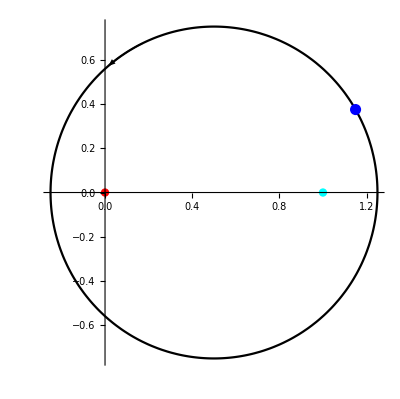

```mathematica
arrowPts2D=Table[ReIm[1/2+3/4 Exp[I t]],{t,Pi/6+1.5,Pi/6+1.75,0.01}];
arrow2D=Graphics@{Black,Arrow[arrowPts2D]};
p02D=Graphics@{PointSize[0.015],Red,Point[{0,0}]};
p12D=Graphics@{PointSize[0.015],Cyan,Point[{1,0}]};
startPt2D=Graphics@{PointSize[0.02],Blue,Point[ReIm[1/2+3/4 Exp[Pi I/6]]]};

 pp1=ParametricPlot[{Re@z,Im@z}/.z->1/2+3/4 Exp[I t],{t,0,2 Pi},PlotStyle->Black];
Show[{pp1,arrow2D,p02D,p12D,startPt2D}]
```

```mathematica
(*
 do black contour in a_2
*)
tStart=Pi/6;
tEnd=2 Pi+Pi/6;
theRoot2F[z_]:=z^(1/2)(1-z)^(1/2);

theZ[t_]:=1/2+1000 Exp[I t];

wStart=theRoot2F[theZ[tStart]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->50];

root2Int=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]
```

-0.785393+0.0000201495 ⅈ

```mathematica
pSeries=w/.AsymptoticSolve[z(1-z)-w^2==0,w,{z,∞,50}];
pSeries/.z->theZ[tStart]//N
Coefficient[pSeries,z,-1]//N
2 Pi I(1/8 I)//N
Beta[3/2,3/2]//N
((2 Pi I(1/8 I))/(Exp[2 Pi I(1/2)]-1))//N
```

{-1.15201+0.516202 ⅈ,1.15201-0.516202 ⅈ}

{0.-0.125 ⅈ,0.+0.125 ⅈ}

-0.785398

0.392699

0.392699

```mathematica
(*
 do black contour in a_2
*)
tStart=Pi/4;
tEnd=2 Pi+Pi/4;
theRoot2F[z_]:=z^(1/2)(1-z)^(1/2);

theZ[t_]:=3/2 Exp[I t];

wStart=theRoot2F[theZ[tStart]];
Print["wStart: ",wStart//N];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->20];
blackInt=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}];
ppBlack1=ParametricPlot3D[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Black}];
(*bluePt=Graphics3D@{PointSize[0.025],Blue,Point@{Re@theR[rStart],Im@theR[rStart],Re@solF2[rStart]}};*)
arrowPts1=Table[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart+1.5,tStart+1.75,0.01}];

startPt3DA=Graphics3D@{PointSize[0.025],Blue,Point[{Re@theZ[tStart],Im@theZ[tStart],Re@solF1[Pi/4]}]};
arrow11=Graphics3D@{Black,Arrowheads[0.04],Arrow[arrowPts1]};

p03D=Graphics3D@{PointSize[0.025],Red,Point[{0,0,0}]};
p13D=Graphics3D@{PointSize[0.025],Cyan,Point[{1,0,0}]};
root2Int=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]

Show[{difPlot,ppBlack1,arrow11,p03D,p13D,startPt3DA},PlotRange->All]
```

wStart: 1.15201-0.516202 ⅈ

-0.785398-1.56308×10^-7 ⅈ

-Graphics3D-

```mathematica
(*
 do black contour in a_2
*)
tStart=Pi/6;
tEnd=2 Pi+Pi/6;
theRoot2F[z_]:=z^(1/2)(1-z)^(1/2);

theZ[t_]:=1/2+1 Exp[I t];

wStart=theRoot2F[theZ[tStart]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->20];
blackInt=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}];
ppYellow=ParametricPlot3D[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Yellow}];
(*bluePt=Graphics3D@{PointSize[0.025],Blue,Point@{Re@theR[rStart],Im@theR[rStart],Re@solF2[rStart]}};*)
arrowPts=Table[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart+1.5,tStart+1.75,0.01}];

startPt3D=Graphics3D@{PointSize[0.02],Blue,Point[{Re@theZ[tStart],Im@theZ[tStart],Re@solF1[Pi/4]}]};
arrow1=Graphics3D@{Yellow,Arrowheads[0.04],Arrow[arrowPts]};

p03D=Graphics3D@{PointSize[0.025],Red,Point[{0,0,0}]};
p13D=Graphics3D@{PointSize[0.025],Cyan,Point[{1,0,0}]};
root2Int=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]

Show[{difPlot,ppYellow,arrow1,p03D,p13D,startPt3D},PlotRange->All]
```

-0.785398+2.37604×10^-8 ⅈ

-Graphics3D-

```mathematica
Show[{sheetA,sheetB,sheetC,sheetD,p03D,p13D,ppBlack1,arrow11,startPt3DA,ppYellow},PlotRange->All]
```

-Graphics3D-

```mathematica
Beta[3/2,3/2]//N
```

0.392699

```mathematica
(*
 do blue contour from mrp to r=2;
*)
rStart=1;
rEnd=2;

theR[r_]:=r Exp[Pi I/6];

wStart3=Exp[2 Pi I(5/7)] theF[theR[rStart]];
wDeriv3=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF3=NDSolveValue[{wDeriv3,w[rStart]==wStart3},w,{r,rStart,rEnd},WorkingPrecision->20];
blueInt=NIntegrate[solF3[r] D[theR[r],r],{r,rStart,rEnd}];
pp3=ParametricPlot3D[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,rStart+0.075,rEnd-0.075},PlotStyle->{Thickness[0.01],Blue}];

orangePt=Graphics3D@{PointSize[0.025],Orange,Point@{Re@theR[rEnd],Im@theR[rEnd],Re@solF3[rEnd]}};
blueArrowPts=Table[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,1.5,1.7,0.01}];
blueArrow1=Graphics3D@{Blue,Arrow[blueArrowPts]};


Show[{root57,pp1,pp2,pp3,greenPt,blackPt,bluePt,arrow1,orangePt,blueArrow1},BoxRatios->{1, 1, 1},AxesLabel->{Style["Re(z)",12,Black,Bold],Style["Im(z)",12,Black,Bold],Style["Re(w)",12,Black,Bold]}]
```

-Graphics3D-

### z^(4/14)(1-z)^(2/7) work

```mathematica
tStart=Pi/6;
tEnd=2 Pi+Pi/6;


theZ[t_]:=2Exp[I t];
wVals=NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->25]

wStart1=wVals[[1]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
pp1=ParametricPlot3D[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.01],Yellow}];

Show[{difPlot,pp1},PlotRange->All]
```

{-1.295459318722770378607878+0.040103767026530561954947 ⅈ,-1.18456888819346409748614-0.52594648750560447322642 ⅈ,-1.149768143413123065697299+0.59821097865863568471498 ⅈ,-0.839060061573414912926687-0.9878265898768871381443352 ⅈ,-0.776351286319605150963798+1.037835169391207840623841 ⅈ,-0.327365099362403340604164-1.254055521224968091674107 ⅈ,-0.24916853564679993871076+1.27190337661278814462 ⅈ,0.24916853564679993871076-1.27190337661278814462 ⅈ,0.327365099362403340604164+1.254055521224968091674107 ⅈ,0.776351286319605150963798-1.037835169391207840623841 ⅈ,0.839060061573414912926687+0.9878265898768871381443352 ⅈ,1.149768143413123065697299-0.59821097865863568471498 ⅈ,1.18456888819346409748614+0.52594648750560447322642 ⅈ,1.295459318722770378607878-0.040103767026530561954947 ⅈ}

-Graphics3D-

```mathematica
solF1[tStart]
solF1[tEnd]
Exp[2 Pi I(4/14)] Exp[2 Pi I(2/7)] solF1[tStart]
```

-1.295459318722770379+0.040103767026530562 ⅈ

1.184568890827979452+0.525946488573494755 ⅈ

1.184568888193464097+0.5259464875056044732 ⅈ

```mathematica
(*
 first extend yellow contour start to outer radial range
*)
rStart=1;
rEnd=2;

ClearAll[theR];
theR[r_]:=r Exp[Pi I/6];

wStart2=wStart1;
wDeriv2=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF2=NDSolveValue[{wDeriv2,w[rStart]==wStart2},w,{r,rStart,rEnd},WorkingPrecision->20];
wAt2=solF2[rEnd]
```

-1.361297584981212273+0.04210310335812488595 ⅈ

```mathematica
(*
 now do red contour starting from wAt2;
*)
rStart=2;
rEnd=1;


theR[r_]:=r Exp[Pi I/6];

wStart2=wAt2;
wDeriv2=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF2=NDSolveValue[{wDeriv2,w[rStart]==wStart2},w,{r,rStart,rEnd},WorkingPrecision->20];
redInt=NIntegrate[solF2[r] D[theR[r],r],{r,rStart,rEnd}];
pp2=ParametricPlot3D[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,rStart-0.075,rEnd+0.075},PlotStyle->{Thickness[0.01],Red}];
bluePt=Graphics3D@{PointSize[0.025],Blue,Point@{Re@theR[rStart],Im@theR[rStart],Re@solF2[rStart]}};
arrowPts=Table[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,1.6,1.5,-0.01}];
arrow1=Graphics3D@{Red,Arrow[arrowPts]};
Show[{difPlot,pp1,pp2,bluePt,arrow1},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 do blue contour from mrp to r=2;
*)
rStart=1;
rEnd=2;

theR[r_]:=r Exp[Pi I/6];

wStart3=Exp[2 Pi I(5/7)] theF[theR[rStart]];
wDeriv3=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF3=NDSolveValue[{wDeriv3,w[rStart]==wStart3},w,{r,rStart,rEnd},WorkingPrecision->20];
blueInt=NIntegrate[solF3[r] D[theR[r],r],{r,rStart,rEnd}];
pp3=ParametricPlot3D[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,rStart+0.075,rEnd-0.075},PlotStyle->{Thickness[0.01],Blue}];

orangePt=Graphics3D@{PointSize[0.025],Orange,Point@{Re@theR[rEnd],Im@theR[rEnd],Re@solF3[rEnd]}};
blueArrowPts=Table[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,1.5,1.7,0.01}];
blueArrow1=Graphics3D@{Blue,Arrow[blueArrowPts]};


Show[{root57,pp1,pp2,pp3,greenPt,blackPt,bluePt,arrow1,orangePt,blueArrow1},BoxRatios->{1, 1, 1},AxesLabel->{Style["Re(z)",12,Black,Bold],Style["Im(z)",12,Black,Bold],Style["Re(w)",12,Black,Bold]}]
```

-Graphics3D-

```mathematica
redInt
blueInt
-Exp[2 Pi I(5/7)] redInt
```

-0.829729-1.04045 ⅈ

0.829729-1.04045 ⅈ

0.829729-1.04045 ⅈ

### z^(1/3)(1-z)^(1/2) work

```mathematica
tStart=Pi/6;
tEnd=4 Pi+Pi/6;


theZ[t_]:=3Exp[I t];
wVals=NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->25]

wStart1=wVals[[1]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
pp1=ParametricPlot3D[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.01],Yellow}];

Show[{difPlot,pp1},PlotRange->All]
```

{-1.706719041191187765051116+0.143430462608100332051078 ⅈ,-1.599932867789290356305278-0.611291257696425830081248 ⅈ,-1.475468576949762997583995+0.869744020733906657946899 ⅈ,-1.17626036803278773023133-1.244939247418889797499104 ⅈ,-0.951983465608854930652096+1.423794108842951726616803 ⅈ,-0.519615076500676911103385-1.632011751012147776165578 ⅈ,-0.239946353593100160941889+1.695844312006829209468703 ⅈ,0.239946353593100160941889-1.695844312006829209468703 ⅈ,0.519615076500676911103385+1.632011751012147776165578 ⅈ,0.951983465608854930652096-1.423794108842951726616803 ⅈ,1.17626036803278773023133+1.244939247418889797499104 ⅈ,1.475468576949762997583995-0.869744020733906657946899 ⅈ,1.599932867789290356305278+0.611291257696425830081248 ⅈ,1.706719041191187765051116-0.143430462608100332051078 ⅈ}

-Graphics3D-

```mathematica
solF1[tStart]
solF1[tEnd]
Exp[4 Pi I(4/14)] Exp[4 Pi I(2/7)] solF1[tStart]
```

-1.706719041191187765+0.143430462608100332 ⅈ

-1.176260362465164609-1.24493924558419039 ⅈ

-1.17626036803278773-1.244939247418889797 ⅈ

```mathematica
(*
 do red contour from mrp to r=2;
*)
rStart=2;
rEnd=1;


theR[r_]:=r Exp[Pi I/6];

wStart2=theF[theR[rStart]];
wDeriv2=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF2=NDSolveValue[{wDeriv2,w[rStart]==wStart2},w,{r,rStart,rEnd},WorkingPrecision->20];
redInt=NIntegrate[solF2[r] D[theR[r],r],{r,rStart,rEnd}];
pp2=ParametricPlot3D[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,rStart-0.075,rEnd+0.075},PlotStyle->{Thickness[0.01],Red}];
bluePt=Graphics3D@{PointSize[0.025],Blue,Point@{Re@theR[rStart],Im@theR[rStart],Re@solF2[rStart]}};
arrowPts=Table[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,1.6,1.5,-0.01}];
arrow1=Graphics3D@{Red,Arrow[arrowPts]};
Show[{sheet1,sheet2,pp1,blackPt,pp2,bluePt,arrow1,greenPt},PlotRange->All]
```

SetDelayed::write: Tag Integer in 2[r_] is Protected.

NDSolveValue::ndinnt: Initial condition (2.[2.])^(5/7) is not a number or a rectangular array of numbers.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NDSolveValue::dsvar: 1.07502 cannot be used as a variable.

NDSolveValue::dsvar: 1.09236 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

NDSolveValue::ndinnt: Initial condition (2.[2.])^(5/7) is not a number or a rectangular array of numbers.

NDSolveValue::dsvar: 1.6 cannot be used as a variable.

NDSolveValue::dsvar: 1.59 cannot be used as a variable.

NDSolveValue::dsvar: 1.58 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

NDSolveValue::ndinnt: Initial condition (2.[2.])^(5/7) is not a number or a rectangular array of numbers.

-Graphics3D-

```mathematica
(*
 do blue contour from mrp to r=2;
*)
rStart=1;
rEnd=2;

theR[r_]:=r Exp[Pi I/6];

wStart3=Exp[2 Pi I(5/7)] theF[theR[rStart]];
wDeriv3=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF3=NDSolveValue[{wDeriv3,w[rStart]==wStart3},w,{r,rStart,rEnd},WorkingPrecision->20];
blueInt=NIntegrate[solF3[r] D[theR[r],r],{r,rStart,rEnd}];
pp3=ParametricPlot3D[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,rStart+0.075,rEnd-0.075},PlotStyle->{Thickness[0.01],Blue}];

orangePt=Graphics3D@{PointSize[0.025],Orange,Point@{Re@theR[rEnd],Im@theR[rEnd],Re@solF3[rEnd]}};
blueArrowPts=Table[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,1.5,1.7,0.01}];
blueArrow1=Graphics3D@{Blue,Arrow[blueArrowPts]};


Show[{root57,pp1,pp2,pp3,greenPt,blackPt,bluePt,arrow1,orangePt,blueArrow1},BoxRatios->{1, 1, 1},AxesLabel->{Style["Re(z)",12,Black,Bold],Style["Im(z)",12,Black,Bold],Style["Re(w)",12,Black,Bold]}]
```

-Graphics3D-

```mathematica
redInt
blueInt
-Exp[2 Pi I(5/7)] redInt
```

-0.829729-1.04045 ⅈ

0.829729-1.04045 ⅈ

0.829729-1.04045 ⅈ

### z^(5/7) work

```mathematica
theF[z_]:=z^(5/7);
sheet1=ParametricPlot3D[{Re@z,Im@z,Re[theF[z]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],sheetColors[[54]]}];
sheet2=ParametricPlot3D[{Re@z,Im@z,Re[Exp[2 Pi I(5/7)] theF[z]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],sheetColors[[61]]}];
root57=Show[{sheet1,sheet2},PlotRange->All]
```

-Graphics3D-

```mathematica
tStart=Pi/6;
tEnd=2 Pi+Pi/6;


theZ[t_]:=Exp[I t];
wVals=theF[theZ[tStart]];

wStart1=wVals;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
pp1=ParametricPlot3D[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart+0.1,tEnd-0.1},PlotStyle->{Thickness[0.01],Yellow}];
blackPt=Graphics3D@{PointSize[0.02],Black,Point@{Re@theZ[tStart],Im@theZ[tStart],Re@solF1[tStart]}};
greenPt=Graphics3D@{PointSize[0.025],Darker@Green,Point@{Re@theZ[tEnd],Im@theZ[tEnd],Re@solF1[tEnd]}};
(*Print["red point: ",solF1[tStart]]
Print["black point: ",solF1[tEnd]]
Print["red point times Exp[2 pi i(1/2)]",Exp[2 Pi I(5/7)] solF1[tStart]];*)
Show[{sheet1,sheet2,pp1,blackPt,greenPt},PlotRange->All]
```

-Graphics3D-

```mathematica
theF[z]
```

z^(5/7)

```mathematica
(*
 do red contour from mrp to r=2;
*)
rStart=2;
rEnd=1;


theR[r_]:=r Exp[Pi I/6];

wStart2=theF[theR[rStart]];
wDeriv2=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF2=NDSolveValue[{wDeriv2,w[rStart]==wStart2},w,{r,rStart,rEnd},WorkingPrecision->20];
redInt=NIntegrate[solF2[r] D[theR[r],r],{r,rStart,rEnd}];
pp2=ParametricPlot3D[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,rStart-0.075,rEnd+0.075},PlotStyle->{Thickness[0.01],Red}];
bluePt=Graphics3D@{PointSize[0.025],Blue,Point@{Re@theR[rStart],Im@theR[rStart],Re@solF2[rStart]}};
arrowPts=Table[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,1.6,1.5,-0.01}];
arrow1=Graphics3D@{Red,Arrow[arrowPts]};
Show[{sheet1,sheet2,pp1,blackPt,pp2,bluePt,arrow1,greenPt},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 do blue contour from mrp to r=2;
*)
rStart=1;
rEnd=2;

theR[r_]:=r Exp[Pi I/6];

wStart3=Exp[2 Pi I(5/7)] theF[theR[rStart]];
wDeriv3=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF3=NDSolveValue[{wDeriv3,w[rStart]==wStart3},w,{r,rStart,rEnd},WorkingPrecision->20];
blueInt=NIntegrate[solF3[r] D[theR[r],r],{r,rStart,rEnd}];
pp3=ParametricPlot3D[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,rStart+0.075,rEnd-0.075},PlotStyle->{Thickness[0.01],Blue}];

orangePt=Graphics3D@{PointSize[0.025],Orange,Point@{Re@theR[rEnd],Im@theR[rEnd],Re@solF3[rEnd]}};
blueArrowPts=Table[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,1.5,1.7,0.01}];
blueArrow1=Graphics3D@{Blue,Arrow[blueArrowPts]};


Show[{root57,pp1,pp2,pp3,greenPt,blackPt,bluePt,arrow1,orangePt,blueArrow1},BoxRatios->{1, 1, 1},AxesLabel->{Style["Re(z)",12,Black,Bold],Style["Im(z)",12,Black,Bold],Style["Re(w)",12,Black,Bold]}]
```

-Graphics3D-

```mathematica
redInt
blueInt
-Exp[2 Pi I(5/7)] redInt
```

-0.829729-1.04045 ⅈ

0.829729-1.04045 ⅈ

0.829729-1.04045 ⅈ

### Square root work

```mathematica
sheet1=ParametricPlot3D[{Re@z,Im@z,Re@Sqrt[z]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],sheetColors[[54]]}];
sheet2=ParametricPlot3D[{Re@z,Im@z,-Re@Sqrt[z]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],sheetColors[[61]]}];
sqrtPlot=Show[{sheet1,sheet2},PlotRange->All]
```

-Graphics3D-

```mathematica
tStart=Pi/6;
tEnd=2 Pi+Pi/6;


theZ[t_]:=Exp[I t];
wVals=NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->25];

wStart1=Sqrt[theZ[tStart]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});

solF1=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
pp1=ParametricPlot3D[{Re@z,Im@z,Re@solF1[t]}/.z->theZ[t],{t,tStart+0.1,tEnd-0.1},PlotStyle->{Thickness[0.01],Yellow}];
blackPt=Graphics3D@{PointSize[0.025],Black,Point@{Re@theZ[tStart],Im@theZ[tStart],Re@solF1[tStart]}};
greenPt=Graphics3D@{PointSize[0.025],Darker@Green,Point@{Re@theZ[tEnd],Im@theZ[tEnd],Re@solF1[tEnd]}};
Print["red point: ",solF1[tStart]]
Print["black point: ",solF1[tEnd]]
Print["red point times Exp[2 pi i(1/2)]",Exp[2 Pi I(1/2)] solF1[tStart]];
Show[{sheet1,sheet2,pp1,blackPt,greenPt},PlotRange->All]
```

red point: 0.9659258262890682867+0.2588190451025207623 ⅈ

black point: -0.9659258261702646248-0.25881904468336612 ⅈ

red point times Exp[2 pi i(1/2)]-0.9659258262890682867-0.2588190451025207623 ⅈ

-Graphics3D-

```mathematica
(*
 do red contour from mrp to r=2;
*)
rStart=2;
rEnd=1;


theR[r_]:=r Exp[Pi I/6];

wStart2=Sqrt[theR[rStart]];
wDeriv2=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theZ[r]});

solF2=NDSolveValue[{wDeriv2,w[rStart]==wStart2},w,{r,rStart,rEnd},WorkingPrecision->20];
redInt=NIntegrate[solF2[r] D[theR[r],r],{r,rStart,rEnd}];
pp2=ParametricPlot3D[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,rStart-0.075,rEnd+0.075},PlotStyle->{Thickness[0.01],Red}];
bluePt=Graphics3D@{PointSize[0.025],Blue,Point@{Re@theR[rStart],Im@theR[rStart],Re@solF2[rStart]}};
arrowPts=Table[{Re@z,Im@z,Re@solF2[r]}/.z->theR[r],{r,1.6,1.5,-0.01}];
arrow1=Graphics3D@{Red,Arrow[arrowPts]};
Show[{sqrtPlot,pp1,pp2,greenPt,blackPt,bluePt,arrow1}]
```

-Graphics3D-

```mathematica
(*
 do blue contour from mrp to r=2;
*)
rStart=1;
rEnd=2;

theR[r_]:=r Exp[Pi I/6];

wStart3=-Sqrt[theR[rStart]];
wDeriv3=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theR[r],r]))/.{w->w[r],z->theR[r]});

solF3=NDSolveValue[{wDeriv3,w[rStart]==wStart3},w,{r,rStart,rEnd},WorkingPrecision->20];
blueInt=NIntegrate[solF3[r] D[theR[r],r],{r,rStart,rEnd}];
pp3=ParametricPlot3D[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,rStart+0.075,rEnd-0.075},PlotStyle->{Thickness[0.01],Blue}];

orangePt=Graphics3D@{PointSize[0.025],Orange,Point@{Re@theR[rEnd],Im@theR[rEnd],Re@solF3[rEnd]}};
blueArrowPts=Table[{Re@z,Im@z,Re@solF3[r]}/.z->theR[r],{r,1.5,1.7,0.01}];
blueArrow1=Graphics3D@{Blue,Arrow[blueArrowPts]};


Show[{sqrtPlot,pp1,pp2,pp3,greenPt,blackPt,bluePt,arrow1,orangePt,blueArrow1},BoxRatios->{1, 1, 1},AxesLabel->{Style["Re(z)",12,Black,Bold],Style["Im(z)",12,Black,Bold],Style["Re(w)",12,Black,Bold]}]
```

-Graphics3D-

```mathematica
redInt
blueInt
```

-0.861929-0.861929 ⅈ

-0.861929-0.861929 ⅈ

### Figure 8 contour over z^{1/2}(1-z)^{1/2}

```mathematica
G[z_]:=z^(1/2)(1-z)^(1/2)

theZ[x_]:=x+1/4 I;
xStart=0;
xEnd=8/10;

wStart=G[theZ[xStart]];
wDeriv=w'[x]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[x],x]))/.{w->w[x],z->theZ[x]});

leg1SolF=NDSolveValue[{wDeriv,w[xStart]==wStart},w,{x,xStart,xEnd},WorkingPrecision->20];
leg2WStart=leg1SolF[xEnd];
leg1Plot=ParametricPlot3D[{Re@z,Im@z,$reim@leg1SolF[x]}/.z->theZ[x],{x,xStart,xEnd},PlotStyle->{Thickness[0.01],Blue}];

Show[{difPlot,leg1Plot},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 leg 2 contour
*)

p1=8/10+1/4 I;
p2=1-1/4 I;
theZ[x_]:=p1(1-x)+p2 x;
xStart=0;
xEnd=1;

wStart=leg2WStart;
wDeriv=w'[x]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[x],x]))/.{w->w[x],z->theZ[x]});

leg2SolF=NDSolveValue[{wDeriv,w[xStart]==wStart},w,{x,xStart,xEnd},WorkingPrecision->20];
leg3WStart=leg2SolF[xEnd];
leg2PlotA=ParametricPlot3D[{Re@z,Im@z,$reim@leg2SolF[x]}/.z->theZ[x],{x,xStart,1/2},PlotStyle->{Thickness[0.01],Blue}];
leg2PlotB=ParametricPlot3D[{Re@z,Im@z,$reim@leg2SolF[x]}/.z->theZ[x],{x,1/2,1},PlotStyle->{Thickness[0.01],Green}];


Show[{difPlot,leg1Plot,leg2PlotA,leg2PlotB},PlotRange->All]
```

NDSolveValue::precw: The precision of the differential equation ({{w'[x]==((1/10-ⅈ/4) (1-2 (Times[«2»]+Times[«2»])))/w[x],w[0]==0.4953987296393966071-0.1513932018306425259 ⅈ},{},{},{},{}}) is less than WorkingPrecision (20.).

-Graphics3D-

```mathematica
(*
 leg 3 contour
*)
theZ[x_]:=1+1/4 Exp[I x];
xStart=-Pi/2;
xEnd=Pi/2;

wStart=leg3WStart;
wDeriv=w'[x]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[x],x]))/.{w->w[x],z->theZ[x]});

leg3SolF=NDSolveValue[{wDeriv,w[xStart]==wStart},w,{x,xStart,xEnd},WorkingPrecision->20];
leg4WStart=leg3SolF[xEnd];
leg3PlotA=ParametricPlot3D[{Re@z,Im@z,$reim@leg3SolF[x]}/.z->theZ[x],{x,xStart,0},PlotStyle->{Thickness[0.01],Green}];
leg3PlotB=ParametricPlot3D[{Re@z,Im@z,$reim@leg3SolF[x]}/.z->theZ[x],{x,0,xEnd},PlotStyle->{Thickness[0.01],Yellow}];


Show[{difPlot,leg1Plot,leg2Plot,leg3PlotA,leg3PlotB},PlotRange->All]
```

NDSolveValue::precw: The precision of the differential equation ({{w'[x]==(ⅈ ⅇ^(ⅈ x) (1-2 (1+Times[«2»])))/(8 w[x]),w[-π/2]==0.4001212946536355024+0.3124052668039895804 ⅈ},{},{},{},{}}) is less than WorkingPrecision (20.).

-Graphics3D-

```mathematica
(*
 leg 4 contour
*)

p1=1+1/4 I;
p2=8/10-1/4 I;
theZ[x_]:=p1(1-x)+p2 x;
xStart=0;
xEnd=1;

wStart=leg4WStart;
wDeriv=w'[x]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[x],x]))/.{w->w[x],z->theZ[x]});

leg4SolF=NDSolveValue[{wDeriv,w[xStart]==wStart},w,{x,xStart,xEnd},WorkingPrecision->20];
leg5WStart=leg4SolF[xEnd];
leg4PlotA=ParametricPlot3D[{Re@z,Im@z,$reim@leg4SolF[x]}/.z->theZ[x],{x,xStart,1/2},PlotStyle->{Thickness[0.01],Yellow}];
leg4PlotB=ParametricPlot3D[{Re@z,Im@z,$reim@leg4SolF[x]}/.z->theZ[x],{x,1/2,xEnd},PlotStyle->{Thickness[0.01],Red}];


Show[{difPlot,leg1Plot,leg2Plot,leg3PlotA,leg3PlotB,leg4PlotA,leg4PlotB},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 leg 5 contour
*)
 theZ[x_]:=x-1/4 I;
xStart=8/10;
xEnd=0;

wStart=leg5WStart;
wDeriv=w'[x]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[x],x]))/.{w->w[x],z->theZ[x]});

leg5SolF=NDSolveValue[{wDeriv,w[xStart]==wStart},w,{x,xStart,xEnd},WorkingPrecision->20];
leg6WStart=leg5SolF[xEnd];
leg5Plot=ParametricPlot3D[{Re@z,Im@z,$reim@leg5SolF[x]}/.z->theZ[x],{x,xStart,xEnd},PlotStyle->{Thickness[0.01],Red}];

Show[{difPlot,leg1Plot,leg2Plot,leg3PlotA,leg3PlotB,leg4PlotA,leg4PlotB,leg5Plot},PlotRange->All]
```

-Graphics3D-

```mathematica
(*
 leg 6 contour
*)
theZ[x_]:=1/4 Exp[I x];
xStart=3Pi/2;
xEnd=Pi/2;

wStart=leg6WStart;
wDeriv=w'[x]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[x],x]))/.{w->w[x],z->theZ[x]});

leg6SolF=NDSolveValue[{wDeriv,w[xStart]==wStart},w,{x,xStart,xEnd},WorkingPrecision->20];

leg6PlotA=ParametricPlot3D[{Re@z,Im@z,$reim@leg6SolF[x]}/.z->theZ[x],{x,xStart,Pi},PlotStyle->{Thickness[0.01],Red}];
leg6PlotB=ParametricPlot3D[{Re@z,Im@z,$reim@leg6SolF[x]}/.z->theZ[x],{x,Pi,xEnd},PlotStyle->{Thickness[0.01],Blue}];


Show[{difPlot,leg1Plot,leg2Plot,leg3PlotA,leg3PlotB,leg4PlotA,leg4PlotB,leg5Plot,leg6PlotA,leg6PlotB},PlotRange->All]
```

NDSolveValue::precw: The precision of the differential equation ({{w'[x]==(ⅈ ⅇ^(ⅈ x) (1-1/2 ⅇ^Times[«2»]))/(8 w[x]),w[(3 π)/2]==-0.4001212942649015965+0.3124052675090628213 ⅈ},{},{},{},{}}) is less than WorkingPrecision (20.).

-Graphics3D-

```mathematica
G[z_]:=z^(1/2)(1-z)^(1/2)
```

```mathematica
rStart=1/100;
rEnd=99/100;


theZ[r_]:=r;
zStart=theZ[rStart];
wVals=NSolveValues[$theFunction==0/.z->theZ[rStart],w,WorkingPrecision->25]
wStart=wVals[[2]];
wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

solF1=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},WorkingPrecision->20];
pp1=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[r]}/.z->theZ[r],{r,rStart,rEnd},PlotStyle->{Thickness[0.01],Blue}];

wStart=wVals[[1]];
wDeriv=w'[r]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[r],r]))/.{w->w[r],z->theZ[r]});

solF2=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},WorkingPrecision->20];
pp2=ParametricPlot3D[{Re@z,Im@z,$reim@solF2[r]}/.z->theZ[r],{r,rStart,rEnd},PlotStyle->{Thickness[0.01],Red}];
Show[{difPlot,pp1,pp2},PlotRange->All]
```

{-0.09949874371066199547344798,0.09949874371066199547344798}

-Graphics3D-

0.1

1.10715

0.05

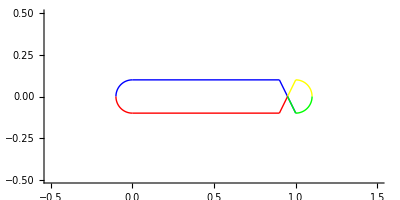

```mathematica
radius1=0.1
 zeroCircle1=Graphics@{Blue,Circle[{0,0},radius1,{Pi/2,Pi}]};
line1=Graphics@{Blue,Line[{{0,0.1},{0.9,0.1}}]};
zeroCircle2=Graphics@{Red,Circle[{0,0},radius1,{Pi,3Pi/2}]};

 oneCircle1=Graphics@{Yellow,Circle[{1,0},radius1,{0,Pi/2}]};
 oneCircle2=Graphics@{Green,Circle[{1,0},radius1,{-Pi/2,0}]};
line2=Graphics@{Red,Line[{{0,-0.1},{0.9,-0.1}}]};

line3=Graphics@{Blue,Line[{{1,-radius1},{0.9,0.1}}]};
theTheta=ArcTan[2]//N
dx=0.1/Tan[theTheta]//N

line4a=Graphics@{Yellow,Line[{{1,radius1},{0.9+dx,0}}]};
line4b=Graphics@{Red,Line[{{0.9,-radius1},{0.9+dx,0}}]};
line4c=Graphics@{Green,Line[{{1,-radius1},{0.9+dx,0}}]};

Show[{zeroCircle1,zeroCircle2,line1,oneCircle1,oneCircle2,line2,line3,line4a,line4b,line4c},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

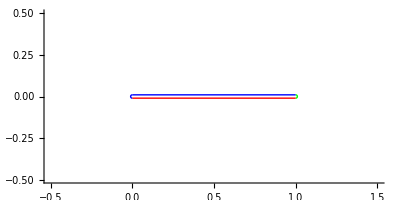

```mathematica
blueLine=Graphics@{Blue,Line[{{0,0.01},{1,0.01}}]};
redLine=Graphics@{Red,Line[{{0,-0.01},{1,-0.01}}]};
circleA=Graphics@{Green,Circle[{1,0},0.01,{-Pi/2,Pi/2}]};
circleB=Graphics@{Blue,Circle[{0,0},0.01,{Pi/2,3Pi/2}]};
Show[{blueLine,redLine,circleA,circleB},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

```mathematica
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];

redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];

yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];

greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
```

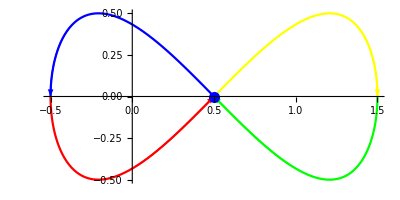

```mathematica
theA=1;
blueArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
redArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-1/2,0,0.025}];
yellowArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2-1/2,Pi/2,0.025}];
greenArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi-1/2,Pi,0.025}];

redArrowG=Graphics@{Red,Arrowheads[0.05],Arrow[redArrowTable]};
blueArrowG=Graphics@{Blue,Arrowheads[0.05],Arrow[blueArrowTable]};
yellowArrowG=Graphics@{Yellow,Arrowheads[0.05],Arrow[yellowArrowTable]};
greenArrowG=Graphics@{Green,Arrowheads[0.05],Arrow[greenArrowTable]};
fig8StartPoint2D=Graphics@{PointSize[0.02],Blue,Point[{1/2,0}]};
p1=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi/2},PlotStyle->Blue];
p2=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,0},PlotStyle->Red];
p3=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,Pi/2},PlotStyle->Yellow];
p4=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi},PlotStyle->Green];

Show[{p1,p2,p3,p4,redArrowG,blueArrowG,yellowArrowG,greenArrowG,fig8StartPoint2D},PlotRange->All]
```

```mathematica
(*
 integrate G(t)=z^(1/2)(1-z)^(1/2) over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;
fig8ContourF[t_,a_]:=(a Sin[t]+1/2)+I a Sin[t] Cos[t];

wStart=G[fig8ContourF[tStart,1]];

wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[fig8ContourF[t,1],t]))/.{w->w[t],z->fig8ContourF[t,1]});
fig8SolF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->20]
intVal=NIntegrate[fig8SolF[t] D[fig8ContourF[t,theA],t],{t,tStart,tEnd}]
```

InterpolatingFunction[…]

-0.785398-1.50503×10^-9 ⅈ

```mathematica
2NIntegrate[G[z],{z,0,1}]
```

0.785398

```mathematica
blueBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi,-Pi/2},PlotStyle->{Blue}];
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
blueArrow3D=Graphics3D@{Blue,Arrowheads[0.05],Arrow[Tube@blueArrowTable3D]};

redBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi/2,0},PlotStyle->{Red}];
redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];
redArrow3D=Graphics3D@{Red,Arrowheads[0.05],Arrow[Tube@redArrowTable3D]};



yellowBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,0,Pi/2},PlotStyle->{Yellow}];
yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];
yellowArrow3D=Graphics3D@{Yellow,Arrowheads[0.05],Arrow[Tube@yellowArrowTable3D]};




greenBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,Pi/2,Pi},PlotStyle->{Green}];
greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
greenArrow3D=Graphics3D@{Green,Arrowheads[0.05],Arrow[Tube@greenArrowTable3D]};
```

```mathematica
startPt3D=Graphics3D@{PointSize[0.035],Blue,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re@fig8SolF[tStart]}]};

startPt3D2=Graphics3D@{PointSize[0.035],Green,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re[Exp[2 Pi I(1/2)]fig8SolF[tStart]]}]};


p03D=Graphics3D@{PointSize[0.025],Red,Point[{0,0,0}]};
p13D=Graphics3D@{PointSize[0.025],Cyan,Point[{1,0,0}]};
(*root2Int=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]
*)

pt1=Show[{difPlot,redBranchPlot,blueBranchPlot,yellowBranchPlot,greenBranchPlot,redArrow3D,blueArrow3D,p03D,p13D,(*startPt3D,*)yellowArrow3D,greenArrow3D(*,startPt3D2*)},BoxRatios->{1, 1, 1},PlotRange->All]
```

-Graphics3D-

### Figure 8 contour over z^{1/3}(1-z)^{4/3}

```mathematica
G[z_]:=z^(1/3)(1-z)^(4/3)
```

```mathematica
tempF[t_,a_,b_,c_]:=(a Sin[t]+b)+I(c Sin[t] Cos[t]);
Manipulate[
ParametricPlot[ReIm@tempF[t,a,b,c],{t,-Pi,Pi},PlotRange->2],
{{a,1},0.5,2},
{{b,1/2},0.1,2},
{{c,1},0.25,2}
]
```

```mathematica
radius1=0.1
 zeroCircle1=Graphics@{Blue,Circle[{0,0},radius1,{Pi/2,Pi}]};
line1=Graphics@{Blue,Line[{{0,0.1},{0.9,0.1}}]};
zeroCircle2=Graphics@{Red,Circle[{0,0},radius1,{Pi,3Pi/2}]};

 oneCircle1=Graphics@{Yellow,Circle[{1,0},radius1,{0,Pi/2}]};
 oneCircle2=Graphics@{Green,Circle[{1,0},radius1,{-Pi/2,0}]};
line2=Graphics@{Red,Line[{{0,-0.1},{0.9,-0.1}}]};

line3=Graphics@{Blue,Line[{{1,-radius1},{0.9,0.1}}]};
theTheta=ArcTan[2]//N
dx=0.1/Tan[theTheta]//N

line4a=Graphics@{Yellow,Line[{{1,radius1},{0.9+dx,0}}]};
line4b=Graphics@{Red,Line[{{0.9,-radius1},{0.9+dx,0}}]};
line4c=Graphics@{Green,Line[{{1,-radius1},{0.9+dx,0}}]};

Show[{zeroCircle1,zeroCircle2,line1,oneCircle1,oneCircle2,line2,line3,line4a,line4b,line4c},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

0.1

1.10715

0.05

-Graphics-

```mathematica
blueLine=Graphics@{Blue,Line[{{0,0.01},{1,0.01}}]};
redLine=Graphics@{Red,Line[{{0,-0.01},{1,-0.01}}]};
circleA=Graphics@{Green,Circle[{1,0},0.01,{-Pi/2,Pi/2}]};
circleB=Graphics@{Blue,Circle[{0,0},0.01,{Pi/2,3Pi/2}]};
Show[{blueLine,redLine,circleA,circleB},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

-Graphics-

```mathematica
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];

redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];

yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];

greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
```

```mathematica
theA=1;
blueArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
redArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-1/2,0,0.025}];
yellowArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2-1/2,Pi/2,0.025}];
greenArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi-1/2,Pi,0.025}];

redArrowG=Graphics@{Red,Arrowheads[0.05],Arrow[redArrowTable]};
blueArrowG=Graphics@{Blue,Arrowheads[0.05],Arrow[blueArrowTable]};
yellowArrowG=Graphics@{Yellow,Arrowheads[0.05],Arrow[yellowArrowTable]};
greenArrowG=Graphics@{Green,Arrowheads[0.05],Arrow[greenArrowTable]};
fig8StartPoint2D=Graphics@{PointSize[0.02],Blue,Point[{1/2,0}]};
p1=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi/2},PlotStyle->Blue];
p2=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,0},PlotStyle->Red];
p3=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,Pi/2},PlotStyle->Yellow];
p4=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi},PlotStyle->Green];

Show[{p1,p2,p3,p4,redArrowG,blueArrowG,yellowArrowG,greenArrowG,fig8StartPoint2D},PlotRange->All]
```

-Graphics-

```mathematica
(*
 integrate G(t)=z^(1/3)(1-z)^(4/3) over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;
fig8ContourF[t_,a_]:=(a Sin[t]+1/2)+I a Sin[t] Cos[t];

wStart=G[fig8ContourF[tStart,1]];

wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[fig8ContourF[t,1],t]))/.{w->w[t],z->fig8ContourF[t,1]});
fig8SolF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->20];
```

```mathematica
blueBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi,-Pi/2},PlotStyle->{Blue}];
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
blueArrow3D=Graphics3D@{Blue,Arrowheads[0.05],Arrow[Tube@blueArrowTable3D]};

redBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi/2,0},PlotStyle->{Red}];
redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];
redArrow3D=Graphics3D@{Red,Arrowheads[0.05],Arrow[Tube@redArrowTable3D]};



yellowBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,0,Pi/2},PlotStyle->{Yellow}];
yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];
yellowArrow3D=Graphics3D@{Yellow,Arrowheads[0.05],Arrow[Tube@yellowArrowTable3D]};




greenBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,Pi/2,Pi},PlotStyle->{Green}];
greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
greenArrow3D=Graphics3D@{Green,Arrowheads[0.05],Arrow[Tube@greenArrowTable3D]};
```

```mathematica
startPt3D=Graphics3D@{PointSize[0.035],Blue,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re@fig8SolF[tStart]}]};

startPt3D2=Graphics3D@{PointSize[0.035],Green,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re[Exp[2 Pi I(1/2)]fig8SolF[tStart]]}]};


p03D=Graphics3D@{PointSize[0.025],Red,Point[{0,0,0}]};
p13D=Graphics3D@{PointSize[0.025],Cyan,Point[{1,0,0}]};
(*root2Int=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]
*)

pt1=Show[{difPlot,redBranchPlot,blueBranchPlot,yellowBranchPlot,greenBranchPlot,redArrow3D,blueArrow3D,p03D,p13D,(*startPt3D,*)yellowArrow3D,greenArrow3D(*,startPt3D2*)},BoxRatios->{1, 1, 1},PlotRange->All]
```

-Graphics3D-

### Figure 8 contour over z^{1/3}(1-z)^{-2/3}

```mathematica
G[z_]:=z^(1/3)(1-z)^(-2/3)
```

```mathematica
tempF[t_,a_,b_,c_]:=(a Sin[t]+b)+I(c Sin[t] Cos[t]);
Manipulate[
ParametricPlot[ReIm@tempF[t,a,b,c],{t,-Pi,Pi},PlotRange->2],
{{a,1},0.5,2},
{{b,1/2},0.1,2},
{{c,1},0.25,2}
]
```

```mathematica
radius1=0.1
 zeroCircle1=Graphics@{Blue,Circle[{0,0},radius1,{Pi/2,Pi}]};
line1=Graphics@{Blue,Line[{{0,0.1},{0.9,0.1}}]};
zeroCircle2=Graphics@{Red,Circle[{0,0},radius1,{Pi,3Pi/2}]};

 oneCircle1=Graphics@{Yellow,Circle[{1,0},radius1,{0,Pi/2}]};
 oneCircle2=Graphics@{Green,Circle[{1,0},radius1,{-Pi/2,0}]};
line2=Graphics@{Red,Line[{{0,-0.1},{0.9,-0.1}}]};

line3=Graphics@{Blue,Line[{{1,-radius1},{0.9,0.1}}]};
theTheta=ArcTan[2]//N
dx=0.1/Tan[theTheta]//N

line4a=Graphics@{Yellow,Line[{{1,radius1},{0.9+dx,0}}]};
line4b=Graphics@{Red,Line[{{0.9,-radius1},{0.9+dx,0}}]};
line4c=Graphics@{Green,Line[{{1,-radius1},{0.9+dx,0}}]};

Show[{zeroCircle1,zeroCircle2,line1,oneCircle1,oneCircle2,line2,line3,line4a,line4b,line4c},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

0.1

1.10715

0.05

-Graphics-

```mathematica
blueLine=Graphics@{Blue,Line[{{0,0.01},{1,0.01}}]};
redLine=Graphics@{Red,Line[{{0,-0.01},{1,-0.01}}]};
circleA=Graphics@{Green,Circle[{1,0},0.01,{-Pi/2,Pi/2}]};
circleB=Graphics@{Blue,Circle[{0,0},0.01,{Pi/2,3Pi/2}]};
Show[{blueLine,redLine,circleA,circleB},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

-Graphics-

```mathematica
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];

redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];

yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];

greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
```

```mathematica
theA=1;
blueArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
redArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-1/2,0,0.025}];
yellowArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2-1/2,Pi/2,0.025}];
greenArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi-1/2,Pi,0.025}];

redArrowG=Graphics@{Red,Arrowheads[0.05],Arrow[redArrowTable]};
blueArrowG=Graphics@{Blue,Arrowheads[0.05],Arrow[blueArrowTable]};
yellowArrowG=Graphics@{Yellow,Arrowheads[0.05],Arrow[yellowArrowTable]};
greenArrowG=Graphics@{Green,Arrowheads[0.05],Arrow[greenArrowTable]};
fig8StartPoint2D=Graphics@{PointSize[0.02],Blue,Point[{1/2,0}]};
p1=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi/2},PlotStyle->Blue];
p2=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,0},PlotStyle->Red];
p3=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,Pi/2},PlotStyle->Yellow];
p4=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi},PlotStyle->Green];

Show[{p1,p2,p3,p4,redArrowG,blueArrowG,yellowArrowG,greenArrowG,fig8StartPoint2D},PlotRange->All]
```

-Graphics-

```mathematica
(*
 integrate G(t)=z^(1/3)(1-z)^(4/3) over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;
fig8ContourF[t_,a_]:=(a Sin[t]+1/2)+I a Sin[t] Cos[t];

wStart=G[fig8ContourF[tStart,1]];

wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[fig8ContourF[t,1],t]))/.{w->w[t],z->fig8ContourF[t,1]});
fig8SolF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->20];
```

```mathematica
blueBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi,-Pi/2},PlotStyle->{Blue}];
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
blueArrow3D=Graphics3D@{Blue,Arrowheads[0.025],Arrow[Tube@blueArrowTable3D]};

redBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi/2,0},PlotStyle->{Red}];
redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];
redArrow3D=Graphics3D@{Red,Arrowheads[0.025],Arrow[Tube@redArrowTable3D]};



yellowBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,0,Pi/2},PlotStyle->{Yellow}];
yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];
yellowArrow3D=Graphics3D@{Yellow,Arrowheads[0.025],Arrow[Tube@yellowArrowTable3D]};




greenBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,Pi/2,Pi},PlotStyle->{Green}];
greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
greenArrow3D=Graphics3D@{Green,Arrowheads[0.025],Arrow[Tube@greenArrowTable3D]};
```

```mathematica
startPt3D=Graphics3D@{PointSize[0.035],Blue,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re@fig8SolF[tStart]}]};

startPt3D2=Graphics3D@{PointSize[0.035],Green,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re[Exp[2 Pi I(1/2)]fig8SolF[tStart]]}]};


p03D=Graphics3D@{PointSize[0.025],Red,Point[{0,0,0}]};
p13D=Graphics3D@{PointSize[0.025],Cyan,Point[{1,0,0}]};
(*root2Int=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]
*)

pt1=Show[{difPlot,redBranchPlot,blueBranchPlot,yellowBranchPlot,greenBranchPlot,redArrow3D,blueArrow3D,p03D,p13D,(*startPt3D,*)yellowArrow3D,greenArrow3D(*,startPt3D2*)},BoxRatios->{1, 1, 1},PlotRange->{{-1,2},Automatic,Automatic}]
```

-Graphics3D-

```mathematica
(*
 integrate f_{39} over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;

theZ[t_]:=(Sin[t]+1/2)+I  Sin[t] Cos[t];

wVals1=Sort@NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->20];
wStart1=G[1/2];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});
solFigure8=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
intVal=NIntegrate[solFigure8[t]D[theZ[t],t],{t,tStart,tEnd},WorkingPrecision->20]
ppa=ParametricPlot3D[{Re@z,Im@z,$reim@solFigure8[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.005],Black}]
1/(Exp[2 Pi I(1/3)]-1) intVal//N
Beta[4/3,1/3]//N
```

-3.9749371843906388332+2.2949310599897258133 ⅈ

-Graphics3D-

2.64996-3.28497×10^-9 ⅈ

2.64996

### Figure 8 contour over z^{1/3}(1-z)^{2/3}

```mathematica
G[z_]:=z^(1/3)(1-z)^(2/3)
```

```mathematica
tempF[t_,a_,b_,c_]:=(a Sin[t]+b)+I(c Sin[t] Cos[t]);
Manipulate[
ParametricPlot[ReIm@tempF[t,a,b,c],{t,-Pi,Pi},PlotRange->2],
{{a,1},0.5,2},
{{b,1/2},0.1,2},
{{c,1},0.25,2}
]
```

```mathematica
radius1=0.1
 zeroCircle1=Graphics@{Blue,Circle[{0,0},radius1,{Pi/2,Pi}]};
line1=Graphics@{Blue,Line[{{0,0.1},{0.9,0.1}}]};
zeroCircle2=Graphics@{Red,Circle[{0,0},radius1,{Pi,3Pi/2}]};

 oneCircle1=Graphics@{Yellow,Circle[{1,0},radius1,{0,Pi/2}]};
 oneCircle2=Graphics@{Green,Circle[{1,0},radius1,{-Pi/2,0}]};
line2=Graphics@{Red,Line[{{0,-0.1},{0.9,-0.1}}]};

line3=Graphics@{Blue,Line[{{1,-radius1},{0.9,0.1}}]};
theTheta=ArcTan[2]//N
dx=0.1/Tan[theTheta]//N

line4a=Graphics@{Yellow,Line[{{1,radius1},{0.9+dx,0}}]};
line4b=Graphics@{Red,Line[{{0.9,-radius1},{0.9+dx,0}}]};
line4c=Graphics@{Green,Line[{{1,-radius1},{0.9+dx,0}}]};

Show[{zeroCircle1,zeroCircle2,line1,oneCircle1,oneCircle2,line2,line3,line4a,line4b,line4c},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

0.1

1.10715

0.05

-Graphics-

```mathematica
blueLine=Graphics@{Blue,Line[{{0,0.01},{1,0.01}}]};
redLine=Graphics@{Red,Line[{{0,-0.01},{1,-0.01}}]};
circleA=Graphics@{Green,Circle[{1,0},0.01,{-Pi/2,Pi/2}]};
circleB=Graphics@{Blue,Circle[{0,0},0.01,{Pi/2,3Pi/2}]};
Show[{blueLine,redLine,circleA,circleB},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

-Graphics-

```mathematica
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];

redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];

yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];

greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
```

```mathematica
theA=1;
blueArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
redArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-1/2,0,0.025}];
yellowArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2-1/2,Pi/2,0.025}];
greenArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi-1/2,Pi,0.025}];

redArrowG=Graphics@{Red,Arrowheads[0.05],Arrow[redArrowTable]};
blueArrowG=Graphics@{Blue,Arrowheads[0.05],Arrow[blueArrowTable]};
yellowArrowG=Graphics@{Yellow,Arrowheads[0.05],Arrow[yellowArrowTable]};
greenArrowG=Graphics@{Green,Arrowheads[0.05],Arrow[greenArrowTable]};
fig8StartPoint2D=Graphics@{PointSize[0.02],Blue,Point[{1/2,0}]};
p1=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi/2},PlotStyle->Blue];
p2=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,0},PlotStyle->Red];
p3=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,Pi/2},PlotStyle->Yellow];
p4=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi},PlotStyle->Green];

Show[{p1,p2,p3,p4,redArrowG,blueArrowG,yellowArrowG,greenArrowG,fig8StartPoint2D},PlotRange->All]
```

-Graphics-

```mathematica
(*
 integrate G(t)=z^(1/3)(1-z)^(2/3) over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;
fig8ContourF[t_,a_]:=(a Sin[t]+1/2)+I a Sin[t] Cos[t];

wStart=G[fig8ContourF[tStart,1]];

wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[fig8ContourF[t,1],t]))/.{w->w[t],z->fig8ContourF[t,1]});
fig8SolF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},WorkingPrecision->20];
```

```mathematica
blueBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi,-Pi/2},PlotStyle->{Blue}];
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-Pi/2-1/2,-Pi/2,0.025}];
blueArrow3D=Graphics3D@{Blue,Arrowheads[0.05],Arrow[Tube@blueArrowTable3D]};

redBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,-Pi/2,0},PlotStyle->{Red}];
redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,-1/2,0,0.025}];
redArrow3D=Graphics3D@{Red,Arrowheads[0.05],Arrow[Tube@redArrowTable3D]};



yellowBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,0,Pi/2},PlotStyle->{Yellow}];
yellowArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi/2-1/2,Pi/2,0.025}];
yellowArrow3D=Graphics3D@{Yellow,Arrowheads[0.05],Arrow[Tube@yellowArrowTable3D]};




greenBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@fig8SolF[t]}/.z->fig8ContourF[t,1],{t,Pi/2,Pi},PlotStyle->{Green}];
greenArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@fig8SolF[t]},{t,Pi-1/2,Pi,0.025}];
greenArrow3D=Graphics3D@{Green,Arrowheads[0.05],Arrow[Tube@greenArrowTable3D]};
```

```mathematica
startPt3D=Graphics3D@{PointSize[0.035],Blue,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re@fig8SolF[tStart]}]};

startPt3D2=Graphics3D@{PointSize[0.035],Green,Point[{Re@fig8ContourF[tStart,1],Im@fig8ContourF[tStart,1],Re[Exp[2 Pi I(1/2)]fig8SolF[tStart]]}]};


p03D=Graphics3D@{PointSize[0.025],Red,Point[{0,0,0}]};
p13D=Graphics3D@{PointSize[0.025],Cyan,Point[{1,0,0}]};
(*root2Int=NIntegrate[solF1[t] D[theZ[t],t],{t,tStart,tEnd}]
*)

pt1=Show[{difPlot,redBranchPlot,blueBranchPlot,yellowBranchPlot,greenBranchPlot,redArrow3D,blueArrow3D,p03D,p13D,(*startPt3D,*)yellowArrow3D,greenArrow3D(*,startPt3D2*)},BoxRatios->{1, 1, 1},PlotRange->{{-1,2},Automatic,Automatic}]
```

-Graphics3D-

```mathematica
(*
 integrate f_{39} over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;

theZ[t_]:=(Sin[t]+1/2)+I  Sin[t] Cos[t];

wVals1=Sort@NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->20];
wStart1=G[1/2];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});
solFigure8=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
intVal=NIntegrate[solFigure8[t]D[theZ[t],t],{t,tStart,tEnd},WorkingPrecision->20]
ppa=ParametricPlot3D[{Re@z,Im@z,$reim@solFigure8[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.005],Black}]
1/(Exp[2 Pi I(1/3)]-1) intVal//N
Beta[4/3,1/3]//N
```

-3.9749371843906388332+2.2949310599897258133 ⅈ

-Graphics3D-

2.64996-3.28497×10^-9 ⅈ

2.64996

### Figure 8 contour over z^{1/3}(1-z)^{1/3}

```mathematica
radius1=0.1
 zeroCircle1=Graphics@{Blue,Circle[{0,0},radius1,{Pi/2,Pi}]};
line1=Graphics@{Blue,Line[{{0,0.1},{0.9,0.1}}]};
zeroCircle2=Graphics@{Red,Circle[{0,0},radius1,{Pi,3Pi/2}]};

 oneCircle1=Graphics@{Yellow,Circle[{1,0},radius1,{0,Pi/2}]};
 oneCircle2=Graphics@{Green,Circle[{1,0},radius1,{-Pi/2,0}]};
line2=Graphics@{Red,Line[{{0,-0.1},{0.9,-0.1}}]};

line3=Graphics@{Blue,Line[{{1,-radius1},{0.9,0.1}}]};
theTheta=ArcTan[2]//N
dx=0.1/Tan[theTheta]//N

line4a=Graphics@{Yellow,Line[{{1,radius1},{0.9+dx,0}}]};
line4b=Graphics@{Red,Line[{{0.9,-radius1},{0.9+dx,0}}]};
line4c=Graphics@{Green,Line[{{1,-radius1},{0.9+dx,0}}]};

Show[{zeroCircle1,zeroCircle2,line1,oneCircle1,oneCircle2,line2,line3,line4a,line4b,line4c},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

0.1

1.10715

0.05

-Graphics-

```mathematica
blueLine=Graphics@{Blue,Line[{{0,0.01},{1,0.01}}]};
redLine=Graphics@{Red,Line[{{0,-0.01},{1,-0.01}}]};
circleA=Graphics@{Green,Circle[{1,0},0.01,{-Pi/2,Pi/2}]};
circleB=Graphics@{Blue,Circle[{0,0},0.01,{Pi/2,3Pi/2}]};
Show[{blueLine,redLine,circleA,circleB},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

-Graphics-

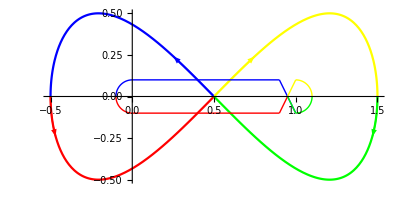

```mathematica
theA=1;
blueArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi+0.25,0.025}];
redArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,-Pi/2+0.25,0.025}];
yellowArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,0.25,0.025}];
greenArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi/2+0.25,0.025}];

redArrowG=Graphics@{Red,Arrowheads[0.05],Arrow[redArrowTable]};
blueArrowG=Graphics@{Blue,Arrowheads[0.05],Arrow[blueArrowTable]};
yellowArrowG=Graphics@{Yellow,Arrowheads[0.05],Arrow[yellowArrowTable]};
greenArrowG=Graphics@{Green,Arrowheads[0.05],Arrow[greenArrowTable]};
p1=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi/2},PlotStyle->Blue];
p2=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,0},PlotStyle->Red];
p3=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,Pi/2},PlotStyle->Yellow];
p4=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi},PlotStyle->Green];
Show[{p1,p2,p3,p4,redArrowG,blueArrowG,yellowArrowG,greenArrowG,zeroCircle1,zeroCircle2,line1,oneCircle1,oneCircle2,line2,line3,line4a,line4b,line4c},PlotRange->All]
```

### Figure 8 contour over z^{1/4}(1-z)^{1/4}

```mathematica
tempF[t_,a_,b_,c_]:=(a Sin[t]+b)+I(c Sin[t] Cos[t]);
Manipulate[
ParametricPlot[ReIm@tempF[t,a,b,c],{t,-Pi,Pi},PlotRange->2],
{{a,1},0.5,2},
{{b,1/2},0.1,2},
{{c,1},0.25,2}
]
```

```mathematica
radius1=0.1
 zeroCircle1=Graphics@{Blue,Circle[{0,0},radius1,{Pi/2,Pi}]};
line1=Graphics@{Blue,Line[{{0,0.1},{0.9,0.1}}]};
zeroCircle2=Graphics@{Red,Circle[{0,0},radius1,{Pi,3Pi/2}]};

 oneCircle1=Graphics@{Yellow,Circle[{1,0},radius1,{0,Pi/2}]};
 oneCircle2=Graphics@{Green,Circle[{1,0},radius1,{-Pi/2,0}]};
line2=Graphics@{Red,Line[{{0,-0.1},{0.9,-0.1}}]};

line3=Graphics@{Blue,Line[{{1,-radius1},{0.9,0.1}}]};
theTheta=ArcTan[2]//N
dx=0.1/Tan[theTheta]//N

line4a=Graphics@{Yellow,Line[{{1,radius1},{0.9+dx,0}}]};
line4b=Graphics@{Red,Line[{{0.9,-radius1},{0.9+dx,0}}]};
line4c=Graphics@{Green,Line[{{1,-radius1},{0.9+dx,0}}]};

Show[{zeroCircle1,zeroCircle2,line1,oneCircle1,oneCircle2,line2,line3,line4a,line4b,line4c},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

0.1

1.10715

0.05

-Graphics-

```mathematica
blueLine=Graphics@{Blue,Line[{{0,0.01},{1,0.01}}]};
redLine=Graphics@{Red,Line[{{0,-0.01},{1,-0.01}}]};
circleA=Graphics@{Green,Circle[{1,0},0.01,{-Pi/2,Pi/2}]};
circleB=Graphics@{Blue,Circle[{0,0},0.01,{Pi/2,3Pi/2}]};
Show[{blueLine,redLine,circleA,circleB},PlotRange->{{-.5,1.5},{-0.5,0.5}},Axes->True]
```

-Graphics-

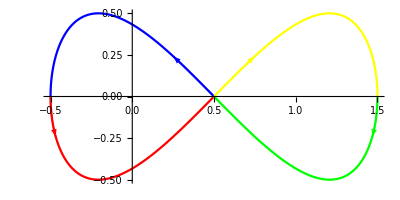

```mathematica
theA=1;
blueArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi+0.25,0.025}];
redArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,-Pi/2+0.25,0.025}];
yellowArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,0.25,0.025}];
greenArrowTable=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi/2+0.25,0.025}];

redArrowG=Graphics@{Red,Arrowheads[0.05],Arrow[redArrowTable]};
blueArrowG=Graphics@{Blue,Arrowheads[0.05],Arrow[blueArrowTable]};
yellowArrowG=Graphics@{Yellow,Arrowheads[0.05],Arrow[yellowArrowTable]};
greenArrowG=Graphics@{Green,Arrowheads[0.05],Arrow[greenArrowTable]};
p1=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi,-Pi/2},PlotStyle->Blue];
p2=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,-Pi/2,0},PlotStyle->Red];
p3=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,0,Pi/2},PlotStyle->Yellow];
p4=ParametricPlot[{theA Sin[t]+0.5,theA Sin[t] Cos[t]},{t,Pi/2,Pi},PlotStyle->Green];
Show[{p1,p2,p3,p4,redArrowG,blueArrowG,yellowArrowG,greenArrowG},PlotRange->All]
```

```mathematica
(*
 integrate G(t)=z^(1/4)(1-z)^(1/4) over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;
theZ[t_]:=(Sin[t]+1/2)+I  Sin[t] Cos[t];
wVals1=Sort@NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->20];

wStart1=wVals1[[1]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});
solF1=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
```

```mathematica
ppa=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.005],Yellow}];
centerPlot=Show[{difPlot,ppa}]
```

-Graphics3D-

```mathematica
(*
 integrate f_{39} over figure-8 contour
*) 
tStart=-Pi;
tEnd=Pi;

theZ[t_]:=(Sin[t]+1/2)+I  Sin[t] Cos[t];

wVals1=Sort@NSolveValues[$theFunction==0/.z->theZ[tStart],w,WorkingPrecision->20];
wStart1=wVals1[[2]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});
solFigure8=NDSolveValue[{wDeriv,w[tStart]==wStart1},w,{t,tStart,tEnd},WorkingPrecision->20];
intVal=NIntegrate[solFigure8[t]D[theZ[t],t],{t,tStart,tEnd},WorkingPrecision->20]
ppa=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->{Thickness[0.005],Black}];
```

{-0.5,0.5}

-0.7853981436976729861-1.5050269706745576251×10^-9 ⅈ

### Draw figure-8 contour over branch

```mathematica
blueBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[t]}/.z->theZ[t],{t,-Pi,-Pi/2},PlotStyle->{Blue}];

redBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[t]}/.z->theZ[t],{t,-Pi/2,0},PlotStyle->{Red}];
yellowBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[t]}/.z->theZ[t],{t,0,Pi/2},PlotStyle->{Yellow}];
greenBranchPlot=ParametricPlot3D[{Re@z,Im@z,$reim@solF1[t]}/.z->theZ[t],{t,Pi/2,Pi},PlotStyle->{Green}];
  blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@solF1[t]},{t,-Pi+1/4,-Pi+1/2,0.025}];
blueArrow3D=Graphics3D@{Blue,Arrowheads[0.05],Arrow[Tube@blueArrowTable3D]};
redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@solF1[t]},{t,-Pi/2+0.2,-Pi/2+0.45,0.025}];
redArrow3D=Graphics3D@{Red,Arrowheads[0.05],Arrow[Tube@redArrowTable3D]};
```

```mathematica
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@solF1[t]},{t,-Pi+1/4,-Pi+1/2,0.025}];
blueArrow3D=Graphics3D@{Blue,Arrowheads[0.05],Arrow[Tube@blueArrowTable3D]};
```

```mathematica
blueArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@solF1[t]},{t,-Pi+1/4,-Pi+1/2,0.025}];
blueArrow3D=Graphics3D@{Blue,Arrowheads[0.05],Arrow[Tube@blueArrowTable3D]};
redArrowTable3D=Table[{theA Sin[t]+0.5,theA Sin[t] Cos[t],$reim@solF1[t]},{t,-Pi/2+0.2,-Pi/2+0.45,0.025}];
redArrow3D=Graphics3D@{Red,Arrowheads[0.05],Arrow[Tube@redArrowTable3D]};
```

```mathematica
re
```

```mathematica
pt1=Show[{difPlot,redBranchPlot,blueBranchPlot,yellowBranchPlot,greenBranchPlot,redArrow3D,blueArrow3D},BoxRatios->{1, 1, 1},PlotRange->All]
pRange=PlotRange@pt1
```

-Graphics3D-

{{-0.989624,1.98062},{-0.983991,0.988497},{-1.09153,1.09153}}

```mathematica
theF[z_]:=z^(1/2)(1-z)^(1/2);
p1=ParametricPlot3D[{Re@z,Im@z,Re@theF[z]}/.z->r Exp[I t],{r,0.01,2},{t,-Pi,0},PlotStyle->{Opacity[0.6],Red}];
p2=ParametricPlot3D[{Re@z,Im@z,-Re@theF[z]}/.z->r Exp[I t],{r,0.01,2},{t,0,Pi},PlotStyle->{Opacity[0.6],Red}];

p3=ParametricPlot3D[{Re@z,Im@z,-Re@theF[z]}/.z->r Exp[I t],{r,0.01,2},{t,-Pi,0},PlotStyle->{Opacity[0.6],Blue}];
p4=ParametricPlot3D[{Re@z,Im@z,Re@theF[z]}/.z->r Exp[I t],{r,0.01,2},{t,0,Pi},PlotStyle->{Opacity[0.6],Blue}];



Show[{p1,p2,p3,p4,redBranchPlot,blueBranchPlot,yellowBranchPlot,greenBranchPlot},PlotRange->All]
```

-Graphics3D-

### Section 9.3: Create the general Pochhammer contour over butterfly plot of testCase0017 (see Sec. 7)

```mathematica
(*
  general pochhammer contour
*)
contourArray={};
pocR1=1/3;
pocR2=1/2;
(*
 do blue contour
*)
 blueContourF[t_]:=(pocR2 I)(1-t)+(1+pocR2 I) t;
blueStartT=0;
blueEndT=1;
blueArrowG=Graphics@{Arrowheads[0.025],Arrow[{ReIm@blueContourF[0.1],ReIm@blueContourF[0.15]}]};
blueContourPlot=ParametricPlot[ReIm@blueContourF[t],{t,blueStartT,blueEndT},AxesOrigin->{0,0},PlotRange->1.5,PlotStyle->{Thickness[0.0025],Blue}];
AppendTo[contourArray,{blueContourF,blueStartT,blueEndT}];
  (*
 do purple contour
*)
 purpleContourF[t_]:=1+pocR2 Exp[I(Pi/2(1-t)+(-Pi/2) t)];
purpleStartT=0;
purpleEndT=1;
purpleContourPlot=ParametricPlot[ReIm@purpleContourF[t],{t,purpleStartT,purpleEndT},PlotStyle->{Thickness[0.0025],Purple},PlotRange->2];

 (* 
 green contour
*)

greenStartT=0;
greenEndT=1;
greenContourF[t_]:=(1-pocR2 I)(1-t)+pocR1 I t;
greenArrowG=Graphics@{Arrowheads[0.025],Arrow[{ReIm@greenContourF[0.1],ReIm@greenContourF[0.15]}]};
greenContourPlot=ParametricPlot[ReIm@greenContourF[t],{t,greenStartT,greenEndT},PlotStyle->{Thickness[0.0025],Darker@Green}];
(*
 do red contour
*)
redContourF[t_]:=pocR1 Exp[I(Pi/2(1-t)+3 Pi/2 t)];
redStartT=0;
redEndT=1;
redContourPlot=ParametricPlot[ReIm@redContourF[t],{t,redStartT,redEndT},PlotStyle->{Thickness[0.0025],Red}];
(*
 do black contour
*)
blackContourF[t_]:=-pocR1 I(1-t)+(1-pocR1 I) t;
blackStartT=0;
blackEndT=1;
blackArrowG=Graphics@{Black,Arrowheads[0.025],Arrow[{ReIm@blackContourF[0.1],ReIm@blackContourF[0.2]}]};
blackContourPlot=ParametricPlot[ReIm@blackContourF[t],{t,blackStartT,blackEndT},PlotStyle->{Thickness[0.0025],Black}];
(*
 do yellow contour
*)
yellowContourF[t_]:=1+pocR1 Exp[I(-Pi/2(1-t)+Pi/2 t)];
yellowStartT=0;
yellowEndT=1;
yellowContourPlot=ParametricPlot[{Re@z,Im@z}/.z->yellowContourF[t],{t,yellowStartT,yellowEndT},PlotStyle->{Thickness[0.0025],Darker@Yellow}];
(*
 do orange contour
*)
 orangeContourF[t_]:=(1+pocR1 I)(1-t)+(-pocR2 I)t
orangeStartT=0;
orangeEndT=1;
orangeArrowG=Graphics@{Black,Arrowheads[0.025],Arrow[{ReIm@orangeContourF[0.1],ReIm@orangeContourF[0.15]}]};
(*orangeContourF[x_]:=theSlope(x-ptSol[[ptIndex,1]])+ptSol[[ptIndex,2]];*)
orangeContourPlot=ParametricPlot[ReIm@orangeContourF[t],{t,orangeStartT,orangeEndT},PlotStyle->{Thickness[0.0025],Orange}];
(*
 do brown contour
*)
brownStartT=0;
brownEndT=1;
 brownContourF[t_]:=pocR2 Exp[(3Pi/2) I(1-t)+(Pi/2 I(t))];
brownContourPlot=ParametricPlot[ReIm@brownContourF[t],{t,0,1},PlotStyle->{Thickness[0.0025],Brown}];
zeroPointG=Graphics@{Blue,PointSize[0.015],Blue,Point[{0,0}]};
onePointG=Graphics@{Blue,PointSize[0.015],Blue,Point[{1,0}]};
```

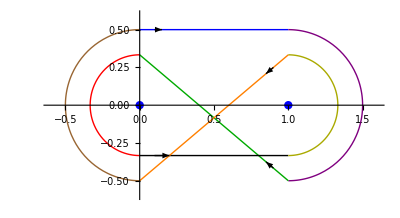

```mathematica
Show[{blueContourPlot,purpleContourPlot,greenContourPlot,redContourPlot,blackContourPlot,yellowContourPlot,orangeContourPlot,brownContourPlot,blueArrowG,greenArrowG,blackArrowG,orangeArrowG,zeroPointG,onePointG},PlotRange->{{-0.6,1.6},{-0.6,0.6}}]
```

### Section 9.4: Create Pochhammer contour over testCase0017 s_2 and s_3 and use the integral over this contour to estimate the integral over the function between s_2 and s_3

```mathematica
(*
 blue contour
*)
sing1=$theSingularList[[2]]//N
blueZ[t_]:=(-1/4-1/2 I)(1-t)+(-1/4+1/2 I)t
wVals=Sort[w/.NSolve[$theFunction==0/.z->blueZ[0],w]]
wStart=wVals[[1]]
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[blueZ[t],t]))/.{w->w[t],z->blueZ[t]});
tStart=0;
tEnd=1;
 blueContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
purpleStartW=blueContourF[tEnd];
pp1=ParametricPlot3D[{Re@z,Im@z,$reim@blueContourF[t]}/.z->blueZ[t],{t,tStart,tEnd},PlotStyle->Blue];
difPlot=Show[{plotTable,pp1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
blueVal=NIntegrate[blueContourF[t] D[blueZ[t],t],{t,0,1}]
```

0.-0.5 ⅈ

{-0.39506+0.476857 ⅈ,-0.140631-3.36476 ⅈ,0.525616-0.477336 ⅈ}

-0.39506+0.476857 ⅈ

-0.650437+0.00593312 ⅈ

```mathematica
(*
 purple contour
*)


 sing3=$theSingularList[[3]]//N
purpleZ[t_]:=sing3+1/4 Exp[I(Pi(1-t))];

wVals=Sort[w/.NSolve[$theFunction==0/.z->purpleZ[0],w]]
wStart=purpleStartW;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[purpleZ[t],t]))/.{w->w[t],z->purpleZ[t]});
tStart=0;
tEnd=1;
 purpleContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
greenWStart=purpleContourF[tEnd];
pp2=ParametricPlot3D[{Re@z,Im@z,$reim@purpleContourF[t]}/.z->purpleZ[t],{t,tStart,tEnd},PlotStyle->Purple];
difPlot=Show[{plotTable,pp1,pp2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
purpleVal=NIntegrate[purpleContourF[t] D[purpleZ[t],t],{t,0,1}]
```

0.+0.5 ⅈ

{-0.39506-0.476857 ⅈ,-0.140631+3.36476 ⅈ,0.525616+0.477336 ⅈ}

0.143799-0.00529821 ⅈ

```mathematica
(*
 green contour
*)

 sing3=$theSingularList[[3]]//N
greenZ[t_]:=(1/4+1/2I)(1-t)+(-1/8-1/2I) t;

wVals=Sort[w/.NSolve[$theFunction==0/.z->greenZ[0],w]]
wStart=greenWStart;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[greenZ[t],t]))/.{w->w[t],z->greenZ[t]});
tStart=0;
tEnd=1;
 greenContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
greenEndW=greenContourF[tEnd];
pp3=ParametricPlot3D[{Re@z,Im@z,$reim@greenContourF[t]}/.z->greenZ[t],{t,tStart,tEnd},PlotStyle->Darker@Green];
difPlot=Show[{plotTable,pp1,pp2,pp3},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
greenVal=NIntegrate[greenContourF[t] D[greenZ[t],t],{t,0,1}]
```

0.+0.5 ⅈ

{-4.65407+2.70018 ⅈ,-0.347818+0.551014 ⅈ,0.33847-0.480457 ⅈ}

-0.585009+0.100318 ⅈ

```mathematica
(*
 red contour
*)


 sing2=$theSingularList[[2]]//N
redZ[t_]:=sing2+1/8 Exp[I(-Pi(1-t))];

wVals=Sort[w/.NSolve[$theFunction==0/.z->redZ[0],w]]
wStart=greenEndW;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[redZ[t],t]))/.{w->w[t],z->redZ[t]});
tStart=0;
tEnd=1;
 redContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
redEndW=redContourF[tEnd];
pp4=ParametricPlot3D[{Re@z,Im@z,$reim@redContourF[t]}/.z->redZ[t],{t,tStart,tEnd},PlotStyle->Red];
difPlot=Show[{plotTable,pp1,pp2,pp3,pp4},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
redVal=NIntegrate[redContourF[t] D[redZ[t],t],{t,0,1}]
```

0.-0.5 ⅈ

{-1.01898-3.98393 ⅈ,-0.303311+0.320553 ⅈ,0.351211-0.3062 ⅈ}

0.0511728+0.00302016 ⅈ

```mathematica
(*
 black contour
*)

blackZ[t_]:=(1/8-1/2 I)(1-t)+(1/8+1/2 I)t
wVals=Sort[w/.NSolve[$theFunction==0/.z->blackZ[0],w]]
wStart=redEndW;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[blackZ[t],t]))/.{w->w[t],z->blackZ[t]});
tStart=0;
tEnd=1;
 blackContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
blackEndW=blackContourF[tEnd];
pp5=ParametricPlot3D[{Re@z,Im@z,$reim@blackContourF[t]}/.z->blackZ[t],{t,tStart,tEnd},PlotStyle->Black];
difPlot=Show[{plotTable,pp1,pp2,pp3,pp4,pp5},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
blackVal=NIntegrate[blackContourF[t] D[blackZ[t],t],{t,0,1}]
```

{-3.63094-3.64986 ⅈ,-0.275935-0.366883 ⅈ,0.257307+0.33421 ⅈ}

-0.542173+0.00547804 ⅈ

```mathematica
(*
 yellow contour
*)


 sing3=$theSingularList[[3]]//N
yellowZ[t_]:=sing3+1/8 Exp[I(Pi t)];

wVals=Sort[w/.NSolve[$theFunction==0/.z->yellowZ[0],w]]
wStart=blackEndW;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[yellowZ[t],t]))/.{w->w[t],z->yellowZ[t]});
tStart=0;
tEnd=1;
 yellowContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
yellowEndW=yellowContourF[tEnd];
pp6=ParametricPlot3D[{Re@z,Im@z,$reim@yellowContourF[t]}/.z->yellowZ[t],{t,tStart,tEnd},PlotStyle->Yellow];
difPlot=Show[{plotTable,pp1,pp2,pp3,pp4,pp5,pp6},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
yellowVal=NIntegrate[yellowContourF[t] D[yellowZ[t],t],{t,0,1}]
```

0.+0.5 ⅈ

{-3.63094+3.64986 ⅈ,-0.275935+0.366883 ⅈ,0.257307-0.33421 ⅈ}

0.0499577-0.00378747 ⅈ

```mathematica
(*
 orange contour
*)


 sing3=$theSingularList[[3]]//N
orangeZ[t_]:=(-1/8+1/2 I)(1-t)+(1/4-1/2 I)t;

wVals=Sort[w/.NSolve[$theFunction==0/.z->orangeZ[0],w]]
wStart=yellowEndW;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[orangeZ[t],t]))/.{w->w[t],z->orangeZ[t]});
tStart=0;
tEnd=1;
 orangeContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
orangeEndW=orangeContourF[tEnd];
pp7=ParametricPlot3D[{Re@z,Im@z,$reim@orangeContourF[t]}/.z->orangeZ[t],{t,tStart,tEnd},PlotStyle->Orange];
difPlot=Show[{plotTable,pp1,pp2,pp3,pp4,pp5,pp6,pp7},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
orangeVal=NIntegrate[orangeContourF[t] D[orangeZ[t],t],{t,0,1}]
```

0.+0.5 ⅈ

{-1.01898+3.98393 ⅈ,-0.303311-0.320553 ⅈ,0.351211+0.3062 ⅈ}

-0.585815-0.116977 ⅈ

```mathematica
(*
 brown contour
*)


 sing2=$theSingularList[[2]]//N
brownZ[t_]:=sing2+1/4 Exp[I(-Pi t)];

wVals=Sort[w/.NSolve[$theFunction==0/.z->brownZ[0],w]]
wStart=orangeEndW;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[brownZ[t],t]))/.{w->w[t],z->brownZ[t]});
tStart=0;
tEnd=1;
 brownContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
brownEndW=brownContourF[tEnd];
pp8=ParametricPlot3D[{Re@z,Im@z,$reim@brownContourF[t]}/.z->brownZ[t],{t,tStart,tEnd},PlotStyle->White];
difPlot=Show[{plotTable,pp1,pp2,pp3,pp4,pp5,pp6,pp7,pp8},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},(*AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},*)FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
brownVal=NIntegrate[brownContourF[t] D[brownZ[t],t],{t,0,1}]
```

0.-0.5 ⅈ

{-4.65407-2.70018 ⅈ,-0.347818-0.551014 ⅈ,0.33847+0.480457 ⅈ}

0.13389+0.0113131 ⅈ

```mathematica
contourSum=blueVal+purpleVal+orangeVal+redVal+blackVal+yellowVal+greenVal+brownVal
integralOverPochhammer=contourSum/((1-Exp[Pi I])(1-Exp[-Pi I]))
```

-1.98461-2.28961×10^-7 ⅈ

-0.496154-5.72403×10^-8 ⅈ

```mathematica
$theSingularList//N
```

{0.,0.-0.5 ⅈ,0.+0.5 ⅈ,-0.477196-0.402475 ⅈ,-0.477196+0.402475 ⅈ,0.199211-0.933168 ⅈ,0.199211+0.933168 ⅈ,1.33333,1.61132-0.550616 ⅈ,1.61132+0.550616 ⅈ}

```mathematica
(* 
first numerically approximate integral from 0 to s_3
*)
 sing2=$theSingularList[[2]];
 sing3=$theSingularList[[3]];
newZ[t_]:=sing3(t);

wVals=Sort[w/.NSolve[$theFunction==0/.z->newZ[0],w,WorkingPrecision->25]]
wStart=wVals[[2]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[newZ[t],t]))/.{w->w[t],z->newZ[t]});
tStart=0;
tEnd=1;
 newContourF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize,WorkingPrecision->20]; 
pp18=ParametricPlot3D[{Re@z,Im@z,$reim@newContourF[t]}/.z->newZ[t],{t,tStart,tEnd},PlotStyle->Black];
difPlot=Show[{plotTable,pp18},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
integralToS3=NIntegrate[newContourF[t] D[newZ[t],t],{t,0,1}]
```

{-0.6324555320336758663997787 ⅈ,0.6324555320336758663997787 ⅈ}

-0.252794+0.00985641 ⅈ

```mathematica
(*
 now approximate integral from 0 to s_2
*)
newZ2[t_]:=sing2(t);

wVals=Sort[w/.NSolve[$theFunction==0/.z->newZ2[0],w,WorkingPrecision->25]]
wStart=wVals[[2]];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (D[newZ2[t],t]))/.{w->w[t],z->newZ2[t]});
tStart=0;
tEnd=1;
 newContourF2=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize,WorkingPrecision->20]; 
pp182=ParametricPlot3D[{Re@z,Im@z,$reim@newContourF2[t]}/.z->newZ2[t],{t,tStart,tEnd},PlotStyle->Red];
difPlot=Show[{plotTable,pp18,pp182},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["Re(z)",12,Bold,Black],Style["Im(z)",12,Bold,Black],Style[ToString@$reim<>"(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},If[$plotLabel,PlotLabel->Row[{Style[$reim,Bold,12,Black]," ",Style[Subscript[s, currentSingIndex],12,Bold,Black],Style[": ",12,Bold,Black],Style[ToString@singularMonodromy,12,Bold,Black]}],
PlotLabel->""
],PlotRange->All(*plotRange*),ImageSize->500]
minusIntegralToS2=-NIntegrate[newContourF2[t] D[newZ2[t],t],{t,0,1}]
integralFromS2ToS3=minusIntegralToS2+integralToS3;
Print["Value over Pochhammer: ",integralOverPochhammer];
Print["Integral from s_2 to s_3: ",integralFromS2ToS3];
Show[{pp18,pp182},BoxRatios->{1, 1, 1},PlotRange->All]
```

{-0.6324555320336758663997787 ⅈ,0.6324555320336758663997787 ⅈ}

-0.243359-0.00629377 ⅈ

Value over Pochhammer: -0.496154-5.72403×10^-8 ⅈ

Integral from s_2 to s_3: -0.496154+0.00356263 ⅈ

## Initialization

```mathematica
(*
 Turn off all operator ligatures for old-style brackets (changes compact brackets to old-style [[]] brackets
*)
CurrentValue[$FrontEnd,{StyleHints,"OperatorRenderings"}]={}



Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]

 $HistoryLength=0;
<<ComputationalGeometry`
 
$radialSegments=13;
$arcSegments=48;

$thetaV=Pi/6;
$singularDelta=1/100;
$annularDelta=1/100;
$opacity=1/2;
$singularPerimeters={};
$singularNorms={};
$singularDistances={};
$annularNorms={};
$colorOffset=37;
 $printMenuDiagnostics=False;

 $segmentsPerCycle=19;
$segmentsPerRing=25;

$acf=20;


(*Needs["PlotLegends`"]*)
DistributeDefinitions[ConvexHull];

 $separationFactor=10;
 $workingPrecision=1000;
 $accuracyComparisonFactor=20;

 $integrationDiagFlag1=False;
 $integrationDiagFlag2=False;
 $removeCSubResidueFactor=50;
 $removableSingularityResidue=50;
 $maxRootVerifyDifference=10^-50;
$selectedAnnulus=1;
$selectedMonodromyIndex=1;
$maxRingRange=1;

 DistributeDefinitions[ z,
 w,
 c,
 s,
 $workingPrecision,
 $separationFactor];


 file::fileExists="File `1` exists.";


(*$convertToNormalFormResidueFactor=10^(-50);*)
$removableNewtonDataResidueFactor=10^(-50);
$integrationDataResidueFactor=10^(-50);
$showNormalizedConstants=False;
$minNSolvePrecision=100;


colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
(*theRGBColors=theColorList/.GrayLevel[azz__]->ColorConvert[GrayLevel[azz],"RGB"];
mycolors=theRGBColors/.RGBColor[az_,bz_,cz_]-> {az,bz,cz};
*)
branchColors=Join[{Red,Blue,Darker@Green,Darker@Yellow,Purple,Orange,Magenta,Pink},Flatten@theColorList[[5;;10]]];

defaultColors={Black,Blue,Brown,Cyan,Gray,Green,Magenta,Orange,Pink,Purple,Red,Yellow};
```

{}

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### getZeroIndexes

```mathematica
getZeroIndexes[theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable},
wKeys=CoefficientRules[theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[theFunction,w,List];
poleFunction=Coefficient[theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$accuracyComparisonFactor;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
poleIndexes
];
```

### getSeriesTypes

```mathematica
getSeriesTypes[baseSeries_,baseSheetLinks_,baseRemovalList_]:=Module[{baseSheetNumbers,seriesLengths,theExpList,minExpList,cycleTypes,multiType,newType,multiBranchType,theLType,minE,type,theD,theN, theTally,mVals,j,typeLoc,i,typeTable,typeLinks },
(*
 uniquely name each branch
*)

baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);
seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];
multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];
 (* 
pick out Taylor series: 
*)
typeTable=Table[
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[Flatten[baseRemovalList[[baseSheetLinks[[1,2]]]][[All,2]]]!={},
(*If[baseRemovalList[[i,2]]!={},*)
(*If[MemberQ[baseRemovableList[[All,1]],baseSheetNumbers[[i]]],*)
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",cycleTypes[[i]],theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",cycleTypes[[i]],theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",cycleTypes[[i]],theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
]; (* theTally,mVals,j,typeLoc,i,typeTable *)
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];
typeLinks=MapThread[{#1,#2}&,{typeTable,baseSheetLinks[[All,2]]}];
{typeTable,baseSheetNumbers,seriesLengths,typeLinks}

];
```

### getRootTestResults

```mathematica
(*
 function for Root Test
*)
getRootTestResults[baseSeries_,baseSheetLinks_,baseSheetNumbers_,theTypeTable_,seriesLengths_,baseSingularPoint_,singularSequence_,theSingularList_,baseSingularIndex_,baseConjList_]:=Module[{cycleBaseSheets,startTerms,plotFlag,totalSheets,graphicsData,at,seriesType,theSeriesNum,cycleType,seriesLength,theexp,lcm,numVals,cList,cTable,lp1,clist,k,dataVals,plotXStart,plotXEnd,endTerms,linearLine,quadraticLine,cubicLine, linearResidue,cubicResidue,quadraticResidue,residueSet,fitSet,bestFitPos,rTest,fitResults,linearPlot,quadraticPlot,cubicPlot,plotSet,fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,fitRadius,rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader,finalReport,c0,c1,c2,c3,estCLSPIndexes,dataTable},

cycleBaseSheets=baseSheetLinks[[All,2,1]];
Print["cycleBaseSheets: ",cycleBaseSheets];

plotFlag=True;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};


at=AbsoluteTiming[
dataTable=Table[
Print["Analyzing base sheet for cycle  ",theBranchNum];
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
                      numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}];

(* 
         start of update k,dataVAls,plotXStart,plotXend,endTerms,linearLine,quadraticLine,cubicLine
 *)
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];

fitResults=rTest;

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
(*
 try getLimLine or LimLine2 fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,baseConjList,fitRadius
*)
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
];



fitRadius=graphicsData[[All,5]];

(*rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
*)
rootTestResults=MapThread[{#1,#2,#3[[1]],#3[[2]],#4,#5}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3[[1]],#3[[2]],#4,#5}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];
(*
 generate convergence report without CLSPs 
*)

nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]];
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)

(*rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];
rootTestReport2=Prepend[rootTestResults2,{"Index","Sheet","Type","Cycle Size","Root Test","est. CLSP","Series size"}];
*)

rootTestResults2=MapThread[{#1,#2,#3[[1]],#3[[2]],SetPrecision[#4,5],#5,#6[[2]]}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];
rootTestReport2=Prepend[rootTestResults2,{Column[{"Generator","Index"},Alignment->Center],"Type","Size",Column[{"Conjugate","Indexes"},Alignment->Center],"R^*",Column[{"Series","size"},Alignment->Center],"estCLSP"}];

rootTestReportHeader=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

finalReport=Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center];
{rootTestResults2,finalReport,estCLSPs,graphicsData,rootTestReportHeader,rootTestReport2}

]; (* end of module *)
```

### getRemovableIndexes

```mathematica
getRemovableIndexes[theFunction_,singPoint_,basePoleList_,baseSeries_,newConjList_,diagFlag_]:=Module[{wVals,oneCycleIndetPos,removableList,oneCyclePos,oneCycleNonPolePos,oneCycleWVals,oneCycleWArray,zDerivs,wDerivs,resultGrid,oneCycleDerivSet},

wVals=DeleteDuplicates[w/.NSolve[theFunction==0/.z->singPoint,w],Abs[#]<10^-$removableSingularityResidue&];


(*
 first choose 1-cycles that are not poles
*)

oneCycleIndetPos={};
removableList={};
oneCyclePos=Position[newConjList,x_/;x==1]//Flatten;
If[diagFlag,
Print["oneCyclePos: ",oneCyclePos];
];
(*
 select all 1-cycle non-pole series 
*)
oneCycleNonPolePos=Select[basePoleList[[oneCyclePos]],#[[2]]=={}&]//Flatten;
If[diagFlag,
Print["oneCycleNonPolePos: ",oneCycleNonPolePos];
];
(*
 compute the value of all 1-cycle non-poles at zero and make array {{index1,wval1},{index2,wval2},{...}}
*)
oneCycleWVals=baseSeries[[oneCycleNonPolePos]]/.z->0;
oneCycleWArray=MapThread[{#1,#2}&,{oneCycleNonPolePos,oneCycleWVals}];
If[diagFlag,
Print["oneCycleWArray: ",oneCycleWArray//N//MatrixForm];
];
(*
 now compute the derivatives at z=singular point and w=series values at 1-cycle non-poles 
*)
zDerivs=D[theFunction,z]/.{z->singPoint,w->#}&/@ oneCycleWArray[[All,2]];
wDerivs=D[theFunction,w]/.{z->singPoint,w->#}&/@ oneCycleWArray[[All,2]];
If[diagFlag,
Print["{zDerivs,wDerivs}: ",MapThread[{#1,#2}&,{zDerivs//N,wDerivs//N}]];
resultGrid=MapThread[{#1[[1]],#1[[2]]//N,#2//N,#3//N}&,{oneCycleWArray,zDerivs,wDerivs}];
Print[Grid[Prepend[resultGrid,{"Index","S(0)","f_z(0,S(0))","f_w(0,S(0))"}],Dividers->{{{True}},{True,True,{False},True}}]];
];
(*
resultGrid,oneCycleDerivSet,
*)


If[Length@oneCycleNonPolePos>0,
oneCycleDerivSet=MapThread[{#1,#2,#3}&,{oneCycleNonPolePos,zDerivs,wDerivs}];
oneCycleIndetPos=Position[oneCycleDerivSet,{a_,b_,c_}/;Abs[b]<10^-20 && Abs[c]<10^-20]//Flatten;
If[Length@oneCycleIndetPos>0,
Print[Style["Found one cycle indeterminants at this singular point",Red]];
resultGrid=MapThread[{#1[[1]],#1[[2]]//N,#2//N,#3//N}&,{oneCycleWArray,zDerivs,wDerivs}];
Print[Grid[Prepend[resultGrid,{"Index","S(0)","f_z(0,S(0))","f_w(0,S(0))"}],Dividers->{{{True}},{True,True,{False},True}}]];
removableList={#[[1]],{#[[2]],#[[3]]}}&/@oneCycleDerivSet[[oneCycleIndetPos]];
Print["removableList: ",removableList//N];
];
];
removableList
];
```

### getIntegrationData

```mathematica
getIntegrationData[baseSingularity_,baseRadius_,nextSingularity_,nextRadius_]:=Module[
{baseSingularPoint,nextSingularPoint,baseNDZ,nextNDZ,baseEqn,nextEqn,p1,p2,eqn3,myPoints,minVal,baseLoc,nextSol,baseSol,nextLoc,theSolvePrec,nextNDZ2,myBasePoints,myNextPoints,otherIndex,singPrecision},

baseSingularPoint=ReIm@baseSingularity;
nextSingularPoint=ReIm@nextSingularity;
singPrecision=Floor@Min@{Precision@baseSingularity,Precision@nextSingularity};
If[singPrecision==∞,
singPrecision=1000;
];
(*
 first check  real parts for vertical case
*)
If[Abs[baseSingularPoint[[1]]-nextSingularPoint[[1]]]<10^-(singPrecision-$accuracyComparisonFactor),
(*
 vertical case, now check imaginary parts to see which one is on top
*)

If[baseSingularPoint[[2]]>nextSingularPoint[[2]],
(*
base above next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]-baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
,
(*
base below next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]+baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
];
,
(* 
non-vertical case
*)
baseEqn=(x-baseSingularPoint[[1]])^2+(y-baseSingularPoint[[2]])^2==baseRadius^2;
nextEqn=(x-nextSingularPoint[[1]])^2+(y-nextSingularPoint[[2]])^2==nextRadius^2;
(*
 get equation of line between singular points
*)

p1=baseSingularPoint;
p2=nextSingularPoint;
eqn3=Expand[y==(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])(x-p1[[1]])+p1[[2]]];
theSolvePrec=Floor@Precision@{baseEqn,nextEqn,eqn3};
If[theSolvePrec<$minNSolvePrecision,
Print[Style["getIntegrationData::solve precision<$minSolvePrecision",Red,14,Bold]];
Abort[];
,
theSolvePrec=$minNSolvePrecision;
];
          baseSol={x,y}/.NSolve[{baseEqn,eqn3},{x,y},WorkingPrecision->theSolvePrec];
nextSol={x,y}/.NSolve[{nextEqn,eqn3},{x,y},WorkingPrecision->theSolvePrec];
myBasePoints=EuclideanDistance[p2,#]&/@baseSol;
minVal=Min@myBasePoints;
baseLoc=Position[myBasePoints,x_/;Abs[x-minVal]<10^-(theSolvePrec-$accuracyComparisonFactor)][[1,1]];
baseNDZ=baseSol[[baseLoc]];
myNextPoints=EuclideanDistance[p1,#]&/@nextSol;
minVal=Min@myNextPoints;
nextLoc=Position[myNextPoints,x_/;Abs[x-minVal]<10^-(theSolvePrec-$accuracyComparisonFactor)][[1,1]];
nextNDZ=nextSol[[nextLoc]];
otherIndex=1;
If[nextLoc==1,
otherIndex=2;
];
nextNDZ2=nextSol[[otherIndex]];

];
{baseNDZ[[1]]+baseNDZ[[2]] I,nextNDZ[[1]]+nextNDZ[[2]]I,nextNDZ2[[1]]+nextNDZ2[[2]]I}
];
```

### aForm

The following aForm code is used verbatim from a question I asked about on the Mathematica Stack Exchange website: https://mathematica.stackexchange.com/questions/267108/constructing-a-specific-polynomial-monomial-ordering-of-fz-w-to-convert-to-l

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```

### integrateOverSheet

```mathematica
integrateOverSheet[startPoint_,singPoint_,startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=singPoint+radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
intTable
];
```

### polishTerms

```mathematica
polishTerms[zVal_,singPoint_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,2]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print["polishTerms error greater than $maxErrorTolerance: ",N[10^-maxErrorTolerance]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### polishSeries

```mathematica
polishSeries[zVal_,singPoint_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,seriesPrec},

wValsPrec=Floor@Precision@zVal;
seriesPrec=Floor@Precision@seriesValues;
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->Min[{wValsPrec,seriesPrec}]];
Print["wVals: ",wVals//N];
polishedValues=Table[
difTable=Abs[seriesValues[[i]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
wVals[[pos]],
{i,1,Length@seriesValues}
];
polishedValues
]
```

### polishBranchValues

```mathematica
polishBranchValues[zVal_,singPoint_,seriesValues_,errorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,seriesPrec},
(* series data format: seriesValues={{indexJ,wValJ},...,{indexN,wValN}} *)
wValsPrec=Floor@Precision@zVal;
seriesPrec=Floor@Precision@seriesValues;
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->Min[{wValsPrec,seriesPrec}]];
polishedValues=Table[
difTable=Abs[seriesValues[[i,2]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-errorTolerance),
Print[Style["polishBranchValues::difTable error exceeded error tolerance of",Purple],Style[HoldForm[10^(-errorTolerance)],Red]];
Print["     difTable: ",difTable//N];
];
{seriesValues[[i,1]],wVals[[pos]]},
{i,1,Length@seriesValues}
];
(* return: {{indexJ,polishWJ},...,{indexN,polishWN}} *)
polishedValues
]
```

### getBranchContinuations

```mathematica
getBranchContinuations[nextSingularIndex_,currentBranchList_,continuationSummary_,diagFlag_]:=Module[{tempBranchList,nextBranch,nextBranchSheets,currentPos,basePoleLinks,nextPoleLinks,nextLinks,tempCLSPList},
tempBranchList={};
tempCLSPList={};
Do[
nextBranch=currentBranchList[[index]];
nextBranchSheets=nextBranch[[2]];
If[diagFlag,
Print["nextBranch: ",nextBranch];
Print["nextBranchSheets: ",nextBranchSheets];
];
(*
 now check if these branch sheets are continuous to last next singular point
*)
(*  *)
currentPos=(Position[continuationSummary[[All,1]],x_/;x==#]&/@ nextBranchSheets)//Flatten ;

basePoleLinks=continuationSummary[[currentPos,3,2]]//Flatten;
nextPoleLinks=continuationSummary[[currentPos,5,2]]//Flatten;
 nextLinks=continuationSummary[[currentPos,4]];

If[diagFlag,
Print["     Branch ",nextBranch," currentContinuationDataPos: ",currentPos];
Print["     basePoleLinks: ",basePoleLinks];
Print["     nextPoleLinks: ",nextPoleLinks];
Print[Style["     nextLinks: ",Red],nextLinks];
];

If[nextLinks==ConstantArray[1,Length@nextBranchSheets]  &&
basePoleLinks=={}  &&
nextPoleLinks=={},
Print[Style["     Branch ",Blue],Style[nextBranch,Blue],Style[" continues onto sing index ",Blue],Style[nextSingularIndex,Blue]];
AppendTo[tempBranchList,nextBranch];
,
Print[Style["     Branch ",Red],Style[nextBranch,Red],Style[" doesn't continue to next sing point",Red],nextSingularIndex];
If[diagFlag,
Print["     assigning ",nextSingularIndex, " to CLSP"];
];
AppendTo[tempCLSPList,{nextBranch,nextSingularIndex}];
],
{index,1,Length@currentBranchList}
];
Print["     tempCLSPList: ",CLSPTable];
Print["     tempBranchList: ",tempBranchList];
{tempBranchList,tempCLSPList}
];
```

### polishBranchTerms

```mathematica
polishBranchTerms[zVal_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,3]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print["polishTerms error greater than $maxErrorTolerance: ",N[10^-maxErrorTolerance]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],terms[[i,2]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### integrateOverAnnulus

```mathematica
integrateOverAnnulus[startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
intTable
];
```

### getAnnularTemplate

```mathematica
getAnnularTemplate[theFunction_]:=Module[{res,theSingularSet,singAccuracy,theSingularList,argList,zeroIndexes,poleIndexes,nearestSing,nearestDist,minRadiusArray,singularPerimeters,absVals,ringSize,tempRings,theAnnuli,ringMemberSingularIndexes,radiiTable,annularSizes,annularCenters,singTable,annulusTable,annulusTableR,ringSizes,minRingSize,tableIndex,j,annulusTableReport,annularTableAnnularIndexes,plottingRadiiTable,newTable,theReturn,annularTableSingularIndexes,i ,theNormDist,thePerimDist,theNearestDistance},




(*totalIntegrationSteps=1500000;*)
(*maxStepSize=0.0001;*)

(*ringDelta=1/20000;*) (* ring separation threshold *)
minRingSize=1/2000;

res=Resultant[theFunction,D[theFunction,w],w];

theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->$workingPrecision],Abs@#1<= Abs@#2&];

(*Print["theSingularSet: ",theSingularSet//N];
Print["Precision of theSingularSet: ",Precision@theSingularSet];*)
singAccuracy=Floor@Accuracy@theSingularSet;
(*Print["singAccuracy: ",singAccuracy];
*)
(*
 final form of the singular list
*)
If[Precision@theSingularSet==∞,
theSingularList=DeleteDuplicates[theSingularSet];
,
(*Print["finite precision"];*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
];
(*Print["Unique singular points: ",theSingularList//N];*)
(*
 get arguments of singular points argList,zeroIndexes,poleIndexes,nearestSing,nearestDist
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles 
*)
poleIndexes=getPoles[theFunction,theSingularList,False];
(*Print["$poleIndexes: ",poleIndexes];*)
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*theNormDist=MapThread[1/2Abs[#1-#2]&,{theSingularList,nearestSing}];
thePerimDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
theNearestDistance=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
$singularPerimeters=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
$singularNorms=MapThread[1/2Abs[#1-#2]&,{theSingularList,nearestSing}];
$singularDistances=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];


For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];


minRadiusArray=nearestDist;
singularPerimeters=minRadiusArray;
,
(*
 in the case of a single singular point, let $singularDistances={10}
*)
Print[Style["Found only one singular point!",Red,Bold]];
$singularDistances={10};
$singularPerimeters={10/3};
$singularNorms={5};

singularPerimeters={10/3};
(*minRadiusArray=∞;*)
];
(* 
compute rings
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];

(*
  compute annular regions 
*)

tempRings=Union[{0},ringSizes,{ringSizes[[-1]]+$maxRingRange}];
theAnnuli=Partition[tempRings,2,1];
ringMemberSingularIndexes=Flatten[Position[theSingularList,x_/;Abs[(Abs[x]-#)]<10^-20]]& /@theAnnuli[[;;-2,2]];
minRingSize=Min[Differences[theAnnuli]];
radiiTable=Table[Array[#&,$radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*
 compute annular sizes
*) 
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
(*annularCenters=(#[[1]]+(#[[2]]-#[[1]])/2)&/@ theAnnuli;
*)
annularCenters=Rationalize[#[[($radialSegments-1)/2+1]],0]&/@ radiiTable;
$annularNorms=Rationalize[#[[($radialSegments-1)/2+1]],0]&/@ radiiTable;

(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,($radialSegments-1)/2+1]],10^-6]*)

(*  *)



singTable={};
annulusTable={};
annulusTableR={};
If[theSingularList[[1]]==0,

(*Print["Routine for singular point at zero"];*)


(* first add 0  *)
If[poleIndexes!={},
If[poleIndexes[[1]]==1,
AppendTo[annulusTable,{" ",1,Style[0,Red],$singularPerimeters[[1]]," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Red],N[$singularPerimeters[[1]]]," "," "," ", {}," "," "}];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];

(* do annulusTable here *)
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
]
,
singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];*)

,
(*
 no singular point at zero
*)
Print["no singular point at zero"];
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
*)
];
(* gives index into annulusTable for an annulus *) annularTableAnnularIndexes=Position[annulusTable,{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_}/;a1==#]&/@ Range[1,Length@theAnnuli]//Flatten;

(* singIndexs gives the row into annulusTable where this singular point is located *)
annularTableSingularIndexes=Position[annulusTable,{x_,y_,z_,a_,b_,c_,d_,e_,f_,g_}/;y==#]&/@Range[1,Length@theSingularList]//Flatten;

plottingRadiiTable=Table[
newTable=radiiTable[[tableIndex]];
newTable[[1]]=newTable[[1]]+(newTable[[2]]-newTable[[1]])/10;
newTable[[-1]]=newTable[[-1]]+(newTable[[-2]]-newTable[[-1]])/10;
newTable,
{tableIndex,1,Length@radiiTable}];

{theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,annularTableAnnularIndexes,annularTableSingularIndexes,plottingRadiiTable,annulusTable,annulusTableR}

];
```

### getSingularMonodromy

```mathematica
(*
 get differential monodromy around a singular point
*)
Options[getSingularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"diagFlag"->False};
getSingularMonodromy[theSingularPoint_,rNorm_,OptionsPattern[]]:=Module[{z0,singularRoots,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles},
Print["nSolveWP: ",OptionValue["nSolveWP"]];
z0=theSingularPoint+rNorm Exp[I $thetaV];
Print["z0: ",z0//N];
singularRoots=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
wArray=MapThread[{#1,#2}&,{Range[Length@singularRoots],singularRoots}];


 branchVals=integrateOverSheet[z0,theSingularPoint,$thetaV,wArray,rNorm,False,OptionValue["integrateWP"]];


polishedVals=polishBranchTerms[z0,branchVals,OptionValue["polishWP"]];
If[OptionValue["diagFlag"],
Print["polishedVals: ",polishedVals//N//MatrixForm];
];
(* *)
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["Monodromy is not consistent!",Purple,14]];
,
Print[Style["Monodromy is consistent",Black,Bold]];
];
{finalCycles,polishedVals}
]
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singulardata.m"}]
(*realPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"realBetaPlot"<>StringTake[testCase,-4;;]<>".m"}]
imagPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"imagBetaPlot"<>StringTake[testCase,-4;;]<>".m"}]*)
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromies.m"}];
annularIntegrationDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularIntegrationData.m"}];
annularMonodromyTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromyTableFileName.m"}];
annularMonodromyTableGraphicsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromyTableGraphics.jpg"}];
singularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularMonodromies.m"}];

annularTableWithMonodromiesFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithMonodromies.m"}];

realPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\realSingularPlot"<>StringTake[testCase,-4;;]<>".m"}];
  imagPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase<>"\\imagSingularPlot"<>StringTake[testCase,-4;;]<>".m"}];
```

### getAnnularMonodromy

```mathematica
(*
 get differential monodromy around a selected annulus
*)
Options[getAnnularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"stiffFlag"->False,"diagFlag"->False};
getAnnularMonodromy[annulusIndex_,annularNorms_,OptionsPattern[]]:=Module[{rNorm,z0,annularMedialVals,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,monodromyTable,annularMonodromy},

(*rNorm=annularNorms[[annulusIndex]];*)
rNorm=$annularNorms[[annulusIndex]];
z0=rNorm Exp[I $thetaV];
If[OptionValue["diagFlag"],
Print["z0: ",z0//N];
];
annularMedialVals=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];
If[OptionValue["diagFlag"],
Print[Grid[SetPrecision[wArray,4]]];
];

 branchVals=integrateOverAnnulus[$thetaV,wArray,rNorm,OptionValue["integrateWP"],OptionValue["stiffFlag"]];
polishedVals=polishBranchTerms[z0,branchVals,20];
If[OptionValue["diagFlag"],
Print[polishedVals//N//MatrixForm];
];
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];
If[OptionValue["diagFlag"],
monodromyTable=MapThread[{#1[[1]],N[#1[[2]],5],N[#1[[3]],5],#2}&,{polishedVals,pArray}];
Print[Grid[monodromyTable]];
];


(* *)
theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
(*
 now sort permutations to standard order
*)
annularMonodromy=sortPermutations[finalCycles];


Print["finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["monodromy is inconsistent!",Red]];
,
Print[Style["monodromy is consistent",Black,Bold]];
];
{z0,rNorm,finalCycles,polishedVals}
];
```

### integrateOverAnnulus

```mathematica
integrateOverAnnulus[startTheta_,w0Table_,radius_,wp_,stiffnessFlag_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});

If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)

{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
(*Print["intTable: ",intTable//N];*)
intTable
];
```

### polishBranchTerms

```mathematica
polishBranchTerms[zVal_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,3]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print[Style["Notice:  polished terms accuracy difference below maxErrorTolerance of "<>ToString[maxErrorTolerance]]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],terms[[i,2]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### getSingTableIndexes

```mathematica
getSingTableIndexes[singTable_,annulus_]:=Module[{singMembers,singIndexes,annulusIndex,return},
If[annulus>Length@theAnnuli || annulus<0,
Print[Style["Annulus number out of range!",Red]];
return=-1;
,
annulusIndex=annularTableAnnularIndexes[[annulus]];
If[annulus==Length@theAnnuli,
singIndexes={-1};
,
singMembers=ringMemberSingularIndexes[[annulus]];
singIndexes=annularTableSingularIndexes[[singMembers]];
];
return={annulusIndex,singIndexes};
];
return
]
```

### sortPermutations

```mathematica
sortPermutations[perm_]:=Module[{rotatedPerm},
rotatedPerm=RotateLeft[#,FirstPosition[#,Min[#]][[1]]-1]&/@ perm;
Sort[rotatedPerm,#1[[1]]<#2[[1]]&]
];
```

### getSingularPoints

```mathematica
(*
 rNormArray is 1/2 distance to either nearest singular point or outer annular value
*)
(*
 $minRadiusArray is 1/3 distance to either nearest singular point or outer annular value
*)
  getSingularPoints[theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDistArray,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck,rNormArray,singularPerimeters,singularNorms,singularDistances
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[$theFunction],Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[theFunction,D[theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$acf)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[theFunction,theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];
minRadiusArray=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
rNormArray=MapThread[1/2Abs[#1-#2]&,{theSingularList,nearestSing}];

singularPerimeters=minRadiusArray;
singularNorms=rNormArray;
singularDistances=nearestDistArray;





For[i=1,i<=Length@nearestDistArray,i++,
If[nearestDistArray[[i]]>10,
nearestDistArray[[i]]=10;
minRadiusArray[[i]]=3;
rNormArray[[i]]=5;
];
];
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray={10/3};
nearestDistArray={10};
rNormArray={5};
singularPerimeters=10/3;
singularNorms=5;
singularDistances=10;

];
theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistArray,rNormArray};
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### polishFunctionValue

```mathematica
Options[polishFunctionValue]={"wp"->MachinePrecision};
  polishFunctionValue[zVal_,wVal_,maxErrorTolerance_,OptionsPattern[]]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec,w},

termsPrec=Floor@Precision@wVal;
wVals=w/.NSolve[$implicitF[zVal,w]==0,w,WorkingPrecision->OptionValue["wp"]];
(*wVals=w/.NSolve[theFunction==0/.z->zVal,w,WorkingPrecision->25];*)
(*Print["wVals: ",wVals//N];*)
difTable=Abs[wVal-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];

wVals[[pos]]

]
```

### getSingularData

```mathematica
getSingularData[testCase_,baseSingularIndex_]:=Module[{baseSingularPoint,baseRadius,dataList,baseBranchTypeArray,baseSeriesMIVPTable,newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,return},

 If[TrueQ@FileExistsQ@seriesFileName[testCase,baseSingularIndex],

baseSingularPoint=$theSingularList[[baseSingularIndex]]; 
baseRadius=$minRadiusArray[[baseSingularIndex]];
(*Print["baseSingularPoint: ",theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[baseSingularIndex]];*)
dataList=Import[seriesFileName[testCase,baseSingularIndex]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList!=11,
Print[Style["This notebook requires Vers.3.0 Puiseux series data with baseSeriesMIVPTable",Red]];
Abort[];
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
(*Print[baseSeries[[All,1;;4]]//N//MatrixForm];*)
return={newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable};
,
Print[Style["Singular file "<>seriesFileName[testCase,baseSingularIndex]<>" not found",Red]];
return=Table[False,{11}];
];
return
];
```

### getSingularMonodromyNew

```mathematica
(*
 get differential monodromy around a singular point
*)
Options[getSingularMonodromyNew]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"diagFlag"->False,"stiffFlag"->False};
getSingularMonodromyNew[theSingularIndex_,rNorm_,OptionsPattern[]]:=Module[{z0,singularRoots,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,flag,theSingularPoint},
(*Print["nSolveWP: ",OptionValue["nSolveWP"]];*)
theSingularPoint=$theSingularList[[theSingularIndex]];
z0=theSingularPoint+rNorm Exp[I $thetaV];
(*Print["z0: ",z0//N];*)
singularRoots=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
wArray=MapThread[{#1,#2}&,{Range[Length@singularRoots],singularRoots}];

 branchVals=integrateOverSheet[z0,theSingularPoint,$thetaV,wArray,rNorm,OptionValue["stiffFlag"],OptionValue["integrateWP"]];


polishedVals=polishBranchTerms[z0,branchVals,OptionValue["polishWP"]];
If[OptionValue["diagFlag"],
Print["     polishedVals: ",polishedVals//N//MatrixForm];
];
(* *)
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
Print["     finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
(*Print[Style["Monodromy is not consistent!",Red]];*)
flag=False;
,
(*Print[Style["Monodromy is consistent"]];*)
flag=True;
];
{finalCycles,polishedVals,{theSingularIndex,flag}}
]
```

### getAnnularMonodromyNew

```mathematica
(*
 get differential monodromy around a selected annulus
*)
Options[getAnnularMonodromyNew]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"stiffFlag"->False,"diagFlag"->False};
getAnnularMonodromyNew[annulusIndex_,annularNorms_,OptionsPattern[]]:=Module[{rNorm,z0,annularMedialVals,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,monodromyTable,flag},

rNorm=annularNorms[[annulusIndex]];
z0=rNorm Exp[I $thetaV];
If[OptionValue["diagFlag"],
Print["z0: ",z0//N];
];
annularMedialVals=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];
If[OptionValue["diagFlag"],
Print[Grid[SetPrecision[wArray,4]]];
];

 branchVals=integrateOverAnnulus[$thetaV,wArray,rNorm,OptionValue["integrateWP"],OptionValue["stiffFlag"]];
polishedVals=polishBranchTerms[z0,branchVals,20];
If[OptionValue["diagFlag"],
Print[polishedVals//N//MatrixForm];
];
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];
If[OptionValue["diagFlag"],
monodromyTable=MapThread[{#1[[1]],N[#1[[2]],5],N[#1[[3]],5],#2}&,{polishedVals,pArray}];
Print[Grid[monodromyTable]];
];


(* *)
theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
Print["     finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
(*Print[Style["monodromy is inconsistent!",Red]];*)
flag=False;
,
(*Print["monodromy is consistent"];*)
flag=True;
];
{finalCycles,polishedVals,{annulusIndex,flag},{z0,rNorm,finalCycles,polishedVals}}
];
```